```mathematica
<<ACPackages`
```

## Построение системы и матриц

### (Получение уравнений см.CurvSystCoor-pseudotor.nb) Определение системы eqsϕr[λ_,ω_,κ_,m_,Re_]

разложенное по модам (с 1-й неверно, т.к. нет зацепления мод)

```mathematica
eqsϕr[λ_,ω_,κ_,m_,Re_]:=Which[m==0,{Re λ ρ vζ[ρ]-vζ'[ρ]-ρ vζ''[ρ],(-1+Re λ ρ^2) ψ'[ρ]+ρ ((1+Re λ ρ^2) ψ''[ρ]-ρ (2 Derivative[3][ψ][ρ]+ρ Derivative[4][ψ][ρ]))},
m==1,{(1+Re λ ρ^2) vζ[ρ]+ρ (ⅈ G Re ρ ψ[ρ]/2-(vζ'[ρ]+ρ vζ''[ρ])),(-3+Re λ ρ^2) ψ[ρ]+ρ ((3-Re λ ρ^2) ψ'[ρ]+ρ (-(3+Re λ ρ^2) ψ''[ρ]+ρ (2 Derivative[3][ψ][ρ]+ρ Derivative[4][ψ][ρ])))},
True,{(m^2+Re λ ρ^2) vζ[ρ]+ρ (ⅈ G m Re ρ ψ[ρ]/2-(vζ'[ρ]+ρ vζ''[ρ])),(m^2 (-4+m^2+Re λ ρ^2) ψ[ρ]+ρ ((1+2 m^2-Re λ ρ^2) ψ'[ρ]-ρ ((1+2 m^2+Re λ ρ^2) ψ''[ρ]-ρ (2 Derivative[3][ψ][ρ]+ρ Derivative[4][ψ][ρ]))))}];
```

текущее: система для ψ и vζ, обрезанная до κ^1
(eqsϕr[λ,ω,κ,G,Re])

```mathematica
nd2=1;
```

```mathematica
eqsϕr[λ_,ω_,κ_,G_,Rn_]:={1/(Re ρ)κ (1/2 G Re ρ^2 Sin[ϕ] ψ[ρ,ϕ]-Sin[ϕ] Derivative[0,1][vζ][ρ,ϕ]+(G Re Rn (-1+ρ^2) (G (4-23 ρ^2+7 ρ^4)+24 (1-5 ρ^2) ω) Sin[ϕ] Derivative[0,1][vζ][ρ,ϕ])/4608-1/4 G Re (-1+ρ^2) Cos[ϕ] Derivative[0,1][ψ][ρ,ϕ]-2 Re ω Cos[ϕ] Derivative[0,1][ψ][ρ,ϕ]+1/737280 G Re (138240 (-1+3 ρ^2)+G^2 Rn^2 (19-120 ρ^2+150 ρ^4-70 ρ^6+9 ρ^8)-40 G Rn^2 (-3+18 ρ^2-20 ρ^4+7 ρ^6) ω) Cos[ϕ] Derivative[0,1][ψ][ρ,ϕ]+ρ Cos[ϕ] Derivative[1,0][vζ][ρ,ϕ]-(G Re Rn ρ (-1+ρ^2)^2 (G (-4+ρ^2)-24 ω) Cos[ϕ] Derivative[1,0][vζ][ρ,ϕ])/4608-1/4 G Re ρ (-1+ρ^2) Sin[ϕ] Derivative[1,0][ψ][ρ,ϕ]-2 Re ρ ω Sin[ϕ] Derivative[1,0][ψ][ρ,ϕ]+1/737280 G Re ρ (-1+ρ^2) (138240+G^2 Rn^2 (-19+21 ρ^2-9 ρ^4+ρ^6)-40 G Rn^2 (3-3 ρ^2+ρ^4) ω) Sin[ϕ] Derivative[1,0][ψ][ρ,ϕ])+κ^2 ((Cos[ϕ]^2 vζ[ρ,ϕ])/Re+(G Rn (-1+ρ^2)^2 (G (-4+ρ^2)-24 ω) Cos[ϕ]^2 vζ[ρ,ϕ])/4608+(Sin[ϕ]^2 vζ[ρ,ϕ])/Re+(G Rn (-1+ρ^2) (G (4-23 ρ^2+7 ρ^4)+24 (1-5 ρ^2) ω) Sin[ϕ]^2 vζ[ρ,ϕ])/4608+1/2 G ρ^2 Cos[ϕ] Sin[ϕ] ψ[ρ,ϕ]-1/737280 G (-1+ρ^2) (138240+G^2 Rn^2 (-19+21 ρ^2-9 ρ^4+ρ^6)-40 G Rn^2 (3-3 ρ^2+ρ^4) ω) Cos[ϕ] Sin[ϕ] ψ[ρ,ϕ]+1/737280 G (138240 (-1+3 ρ^2)+G^2 Rn^2 (19-120 ρ^2+150 ρ^4-70 ρ^6+9 ρ^8)-40 G Rn^2 (-3+18 ρ^2-20 ρ^4+7 ρ^6) ω) Cos[ϕ] Sin[ϕ] ψ[ρ,ϕ]-(Cos[ϕ] Sin[ϕ] Derivative[0,1][vζ][ρ,ϕ])/Re-(G Rn (-1+ρ^2)^2 (G (-4+ρ^2)-24 ω) Cos[ϕ] Sin[ϕ] Derivative[0,1][vζ][ρ,ϕ])/4608+1/59454259200 G nd2 Rn (-1+ρ^2) (G^3 Rn^2 (-4979+20521 ρ^2-13499 ρ^4+4421 ρ^6-829 ρ^8+35 ρ^10)-193536000 (-1+3 ρ^2) ω-16 G^2 Rn^2 (3111-11789 ρ^2+5536 ρ^4-1184 ρ^6+216 ρ^8) ω-6720 G (-10752+17 Rn^2 ω^2+5 Rn^2 ρ^6 ω^2+ρ^2 (38784-55 Rn^2 ω^2)+ρ^4 (-13056+5 Rn^2 ω^2))) Sin[2 ϕ] Derivative[0,1][vζ][ρ,ϕ]-1/4 G (-1+ρ^2) Cos[ϕ]^2 Derivative[0,1][ψ][ρ,ϕ]-1/737280 G (-1+ρ^2) (138240+G^2 Rn^2 (-19+21 ρ^2-9 ρ^4+ρ^6)-40 G Rn^2 (3-3 ρ^2+ρ^4) ω) Cos[ϕ]^2 Derivative[0,1][ψ][ρ,ϕ]+1/59929893273600 G nd2 (8820 (G^4 Rn^4 (-1+ρ^2)^3 (76-103 ρ^2+57 ρ^4-13 ρ^6+ρ^8)+184320 G Rn^2 (-35+60 ρ^2-30 ρ^4+ρ^6) ω-8 G^3 Rn^4 (-1+ρ^2)^3 (-117+138 ρ^2-62 ρ^4+8 ρ^6) ω-35389440 (42+Rn^2 ω^2+Rn^2 ρ^4 ω^2-2 ρ^2 (33+Rn^2 ω^2))+192 G^2 Rn^2 (5 Rn^2 ρ^10 ω^2+ρ^4 (2880-95 Rn^2 ω^2)+60 ρ^2 (-28+Rn^2 ω^2)+15 ρ^6 (-96+5 Rn^2 ω^2)-6 ρ^8 (-28+5 Rn^2 ω^2)-3 (168+5 Rn^2 ω^2)))+(G^4 Rn^4 (-145690+771792 ρ^2-1244565 ρ^4+980784 ρ^6-448350 ρ^8+131544 ρ^10-20727 ρ^12+1280 ρ^14)-325140480 G Rn^2 (-101+380 ρ^2-330 ρ^4+84 ρ^6) ω-252 G^3 Rn^4 (6017-31504 ρ^2+49530 ρ^4-36960 ρ^6+15050 ρ^8-3552 ρ^10+329 ρ^12) ω+26011238400 (9 Rn^2 ρ^4 ω^2+5 (-72+Rn^2 ω^2)-16 ρ^2 (-45+Rn^2 ω^2))+4032 G^2 Rn^2 (777840-923 Rn^2 ω^2+288 Rn^2 ρ^10 ω^2+5040 ρ^6 (-448+Rn^2 ω^2)-1750 ρ^8 (-192+Rn^2 ω^2)+280 ρ^2 (-12912+17 Rn^2 ω^2)-315 ρ^4 (-14544+23 Rn^2 ω^2))) Cos[2 ϕ]) Derivative[0,1][ψ][ρ,ϕ]+(ρ Cos[ϕ]^2 Derivative[1,0][vζ][ρ,ϕ])/Re-1/59454259200 G nd2 Rn ρ (-1+ρ^2)^2 (G^3 Rn^2 (4979-2792 ρ^2+777 ρ^4-134 ρ^6+5 ρ^8)-193536000 ω-16 G^2 Rn^2 (-3111+1228 ρ^2-208 ρ^4+36 ρ^6) ω-6720 G (10752-17 Rn^2 ω^2+Rn^2 ρ^4 ω^2+2 ρ^2 (-1632+Rn^2 ω^2))) Cos[2 ϕ] Derivative[1,0][vζ][ρ,ϕ]-(G Rn ρ (-1+ρ^2)^2 (G (-4+ρ^2)-24 ω) Sin[ϕ]^2 Derivative[1,0][vζ][ρ,ϕ])/4608-1/737280 G ρ (-1+ρ^2) (138240+G^2 Rn^2 (-19+21 ρ^2-9 ρ^4+ρ^6)-40 G Rn^2 (3-3 ρ^2+ρ^4) ω) Cos[ϕ] Sin[ϕ] Derivative[1,0][ψ][ρ,ϕ]-1/8 G ρ (-1+ρ^2) Sin[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]+1/59929893273600 G nd2 ρ (-1+ρ^2) (G^4 Rn^4 (145690-240206 ρ^2+174649 ρ^4-70547 ρ^6+19123 ρ^8-2801 ρ^10+160 ρ^12)-325140480 G Rn^2 (101-89 ρ^2+21 ρ^4) ω-252 G^3 Rn^4 (-6017+9735 ρ^2-6775 ρ^4+2465 ρ^6-545 ρ^8+47 ρ^10) ω+26011238400 (360+Rn^2 (-5+3 ρ^2) ω^2)+4032 G^2 Rn^2 (-777840+923 Rn^2 ω^2+48 Rn^2 ρ^8 ω^2+ρ^2 (1029840-1457 Rn^2 ω^2)+ρ^6 (67200-302 Rn^2 ω^2)+ρ^4 (-497280+958 Rn^2 ω^2))) Sin[2 ϕ] Derivative[1,0][ψ][ρ,ϕ])+1/(2 Re ρ^2)(2 Re λ ρ^2 vζ[ρ,ϕ]+G Re ρ^2 Derivative[0,1][ψ][ρ,ϕ]-2 (Derivative[0,2][vζ][ρ,ϕ]+ρ (Derivative[1,0][vζ][ρ,ϕ]+ρ Derivative[2,0][vζ][ρ,ϕ]))),1/(Re ρ^4)(4 Derivative[0,2][ψ][ρ,ϕ]-Re λ ρ^2 Derivative[0,2][ψ][ρ,ϕ]+Derivative[0,4][ψ][ρ,ϕ]+ρ Derivative[1,0][ψ][ρ,ϕ]-Re λ ρ^3 Derivative[1,0][ψ][ρ,ϕ]-2 ρ Derivative[1,2][ψ][ρ,ϕ]-ρ^2 Derivative[2,0][ψ][ρ,ϕ]-Re λ ρ^4 Derivative[2,0][ψ][ρ,ϕ]+2 ρ^2 Derivative[2,2][ψ][ρ,ϕ]+2 ρ^3 Derivative[3,0][ψ][ρ,ϕ]+1/4608 κ ρ (-4608 G Re ρ^4 Sin[ϕ] vζ[ρ,ϕ]-2304 Re ρ^2 (G (-1+ρ^2)+4 ω) Cos[ϕ] Derivative[0,1][vζ][ρ,ϕ]+72 G^2 Re Rn ρ^2 Sin[ϕ] Derivative[0,1][ψ][ρ,ϕ]-4608 Re λ ρ^2 Sin[ϕ] Derivative[0,1][ψ][ρ,ϕ]-432 G^2 Re Rn ρ^4 Sin[ϕ] Derivative[0,1][ψ][ρ,ϕ]+240 G^2 Re Rn ρ^6 Sin[ϕ] Derivative[0,1][ψ][ρ,ϕ]+384 G Re Rn ρ^2 ω Sin[ϕ] Derivative[0,1][ψ][ρ,ϕ]-1728 G Re Rn ρ^4 ω Sin[ϕ] Derivative[0,1][ψ][ρ,ϕ]+18432 Cos[ϕ] Derivative[0,2][ψ][ρ,ϕ]+8 G^2 Re Rn Cos[ϕ] Derivative[0,2][ψ][ρ,ϕ]-18 G^2 Re Rn ρ^2 Cos[ϕ] Derivative[0,2][ψ][ρ,ϕ]+12 G^2 Re Rn ρ^4 Cos[ϕ] Derivative[0,2][ψ][ρ,ϕ]-2 G^2 Re Rn ρ^6 Cos[ϕ] Derivative[0,2][ψ][ρ,ϕ]+48 G Re Rn ω Cos[ϕ] Derivative[0,2][ψ][ρ,ϕ]-96 G Re Rn ρ^2 ω Cos[ϕ] Derivative[0,2][ψ][ρ,ϕ]+48 G Re Rn ρ^4 ω Cos[ϕ] Derivative[0,2][ψ][ρ,ϕ]+9216 Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]+4 G^2 Re Rn Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]-27 G^2 Re Rn ρ^2 Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]+30 G^2 Re Rn ρ^4 Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]-7 G^2 Re Rn ρ^6 Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]+24 G Re Rn ω Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]-144 G Re Rn ρ^2 ω Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]+120 G Re Rn ρ^4 ω Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]+2304 G Re ρ^3 Sin[ϕ] Derivative[1,0][vζ][ρ,ϕ]-2304 G Re ρ^5 Sin[ϕ] Derivative[1,0][vζ][ρ,ϕ]-9216 Re ρ^3 ω Sin[ϕ] Derivative[1,0][vζ][ρ,ϕ]+9216 ρ Cos[ϕ] Derivative[1,0][ψ][ρ,ϕ]+4 G^2 Re Rn ρ Cos[ϕ] Derivative[1,0][ψ][ρ,ϕ]-81 G^2 Re Rn ρ^3 Cos[ϕ] Derivative[1,0][ψ][ρ,ϕ]+4608 Re λ ρ^3 Cos[ϕ] Derivative[1,0][ψ][ρ,ϕ]+150 G^2 Re Rn ρ^5 Cos[ϕ] Derivative[1,0][ψ][ρ,ϕ]-49 G^2 Re Rn ρ^7 Cos[ϕ] Derivative[1,0][ψ][ρ,ϕ]+24 G Re Rn ρ ω Cos[ϕ] Derivative[1,0][ψ][ρ,ϕ]-432 G Re Rn ρ^3 ω Cos[ϕ] Derivative[1,0][ψ][ρ,ϕ]+600 G Re Rn ρ^5 ω Cos[ϕ] Derivative[1,0][ψ][ρ,ϕ]+9216 ρ Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]+4 G^2 Re Rn ρ Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]-27 G^2 Re Rn ρ^3 Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]+30 G^2 Re Rn ρ^5 Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]-7 G^2 Re Rn ρ^7 Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]+24 G Re Rn ρ ω Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]-144 G Re Rn ρ^3 ω Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]+120 G Re Rn ρ^5 ω Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]-9216 ρ Cos[ϕ] Derivative[1,2][ψ][ρ,ϕ]-4 G^2 Re Rn ρ Cos[ϕ] Derivative[1,2][ψ][ρ,ϕ]+9 G^2 Re Rn ρ^3 Cos[ϕ] Derivative[1,2][ψ][ρ,ϕ]-6 G^2 Re Rn ρ^5 Cos[ϕ] Derivative[1,2][ψ][ρ,ϕ]+G^2 Re Rn ρ^7 Cos[ϕ] Derivative[1,2][ψ][ρ,ϕ]-24 G Re Rn ρ ω Cos[ϕ] Derivative[1,2][ψ][ρ,ϕ]+48 G Re Rn ρ^3 ω Cos[ϕ] Derivative[1,2][ψ][ρ,ϕ]-24 G Re Rn ρ^5 ω Cos[ϕ] Derivative[1,2][ψ][ρ,ϕ]-9216 ρ^2 Cos[ϕ] Derivative[2,0][ψ][ρ,ϕ]-4 G^2 Re Rn ρ^2 Cos[ϕ] Derivative[2,0][ψ][ρ,ϕ]+9 G^2 Re Rn ρ^4 Cos[ϕ] Derivative[2,0][ψ][ρ,ϕ]-6 G^2 Re Rn ρ^6 Cos[ϕ] Derivative[2,0][ψ][ρ,ϕ]+G^2 Re Rn ρ^8 Cos[ϕ] Derivative[2,0][ψ][ρ,ϕ]-24 G Re Rn ρ^2 ω Cos[ϕ] Derivative[2,0][ψ][ρ,ϕ]+48 G Re Rn ρ^4 ω Cos[ϕ] Derivative[2,0][ψ][ρ,ϕ]-24 G Re Rn ρ^6 ω Cos[ϕ] Derivative[2,0][ψ][ρ,ϕ]+9216 ρ^2 Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]+4 G^2 Re Rn ρ^2 Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]-27 G^2 Re Rn ρ^4 Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]+30 G^2 Re Rn ρ^6 Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]-7 G^2 Re Rn ρ^8 Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]+24 G Re Rn ρ^2 ω Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]-144 G Re Rn ρ^4 ω Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]+120 G Re Rn ρ^6 ω Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]-9216 ρ^3 Cos[ϕ] Derivative[3,0][ψ][ρ,ϕ]-4 G^2 Re Rn ρ^3 Cos[ϕ] Derivative[3,0][ψ][ρ,ϕ]+9 G^2 Re Rn ρ^5 Cos[ϕ] Derivative[3,0][ψ][ρ,ϕ]-6 G^2 Re Rn ρ^7 Cos[ϕ] Derivative[3,0][ψ][ρ,ϕ]+G^2 Re Rn ρ^9 Cos[ϕ] Derivative[3,0][ψ][ρ,ϕ]-24 G Re Rn ρ^3 ω Cos[ϕ] Derivative[3,0][ψ][ρ,ϕ]+48 G Re Rn ρ^5 ω Cos[ϕ] Derivative[3,0][ψ][ρ,ϕ]-24 G Re Rn ρ^7 ω Cos[ϕ] Derivative[3,0][ψ][ρ,ϕ])+1/59454259200 κ^2 ρ^2 (-322560 G Re ρ^4 (161280+G^2 Rn^2 (-20+30 ρ^2-15 ρ^4+2 ρ^6)-20 G Rn^2 (6-8 ρ^2+3 ρ^4) ω) Sin[2 ϕ] vζ[ρ,ϕ]-309657600 Re ρ^2 (-192 λ-3 G^2 Rn (1-4 ρ^2+2 ρ^4)+16 G Rn (-1+3 ρ^2) ω+2 G Rn ρ^2 (G (-3+2 ρ^2)-12 ω) Cos[2 ϕ]) ψ[ρ,ϕ]+52022476800 G Re ρ^2 Cos[ϕ]^2 Derivative[0,1][vζ][ρ,ϕ]-3064320 G^3 Re Rn^2 ρ^2 Cos[ϕ]^2 Derivative[0,1][vζ][ρ,ϕ]-52022476800 G Re ρ^4 Cos[ϕ]^2 Derivative[0,1][vζ][ρ,ϕ]+6451200 G^3 Re Rn^2 ρ^4 Cos[ϕ]^2 Derivative[0,1][vζ][ρ,ϕ]-4838400 G^3 Re Rn^2 ρ^6 Cos[ϕ]^2 Derivative[0,1][vζ][ρ,ϕ]+1612800 G^3 Re Rn^2 ρ^8 Cos[ϕ]^2 Derivative[0,1][vζ][ρ,ϕ]-161280 G^3 Re Rn^2 ρ^10 Cos[ϕ]^2 Derivative[0,1][vζ][ρ,ϕ]-19353600 G^2 Re Rn^2 ρ^2 ω Cos[ϕ]^2 Derivative[0,1][vζ][ρ,ϕ]+38707200 G^2 Re Rn^2 ρ^4 ω Cos[ϕ]^2 Derivative[0,1][vζ][ρ,ϕ]-25804800 G^2 Re Rn^2 ρ^6 ω Cos[ϕ]^2 Derivative[0,1][vζ][ρ,ϕ]+6451200 G^2 Re Rn^2 ρ^8 ω Cos[ϕ]^2 Derivative[0,1][vζ][ρ,ϕ]-59454259200 Re λ ρ^2 Cos[ϕ] Sin[ϕ] Derivative[0,1][ψ][ρ,ϕ]+51609600 G^2 Re Rn ρ^6 Cos[ϕ] Sin[ϕ] Derivative[0,1][ψ][ρ,ϕ]+619315200 G Re Rn ω Cos[ϕ] Sin[ϕ] Derivative[0,1][ψ][ρ,ϕ]-619315200 G Re Rn ρ^4 ω Cos[ϕ] Sin[ϕ] Derivative[0,1][ψ][ρ,ϕ]-59454259200 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]+51609600 G^2 Re Rn Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]+1997291520 G^2 nd2 Re Rn ρ^2 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]-153000 G^4 nd2 Re Rn^3 ρ^2 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]-77414400 G^2 Re Rn ρ^4 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]-7431782400 G^2 nd2 Re Rn ρ^4 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]+725760 G^4 nd2 Re Rn^3 ρ^4 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]+3948134400 G^2 nd2 Re Rn ρ^6 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]-806400 G^4 nd2 Re Rn^3 ρ^6 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]+403200 G^4 nd2 Re Rn^3 ρ^8 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]-100800 G^4 nd2 Re Rn^3 ρ^10 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]+5760 G^4 nd2 Re Rn^3 ρ^12 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]+4644864000 G nd2 Re Rn ρ^2 ω Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]-1430400 G^3 nd2 Re Rn^3 ρ^2 ω Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]-12386304000 G nd2 Re Rn ρ^4 ω Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]+5913600 G^3 nd2 Re Rn^3 ρ^4 ω Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]-4838400 G^3 nd2 Re Rn^3 ρ^6 ω Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]+1720320 G^3 nd2 Re Rn^3 ρ^8 ω Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]-403200 G^3 nd2 Re Rn^3 ρ^10 ω Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]-2903040 G^2 nd2 Re Rn^3 ρ^2 ω^2 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]+8601600 G^2 nd2 Re Rn^3 ρ^4 ω^2 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]-2580480 G^2 nd2 Re Rn^3 ρ^8 ω^2 Sin[2 ϕ] Derivative[0,1][ψ][ρ,ϕ]+118908518400 Cos[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]-51609600 G^2 Re Rn Cos[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]+116121600 G^2 Re Rn ρ^2 Cos[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]-77414400 G^2 Re Rn ρ^4 Cos[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]+12902400 G^2 Re Rn ρ^6 Cos[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]-309657600 G Re Rn ω Cos[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]+619315200 G Re Rn ρ^2 ω Cos[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]-309657600 G Re Rn ρ^4 ω Cos[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]+144506880 G^2 nd2 Re Rn Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-9958 G^4 nd2 Re Rn^3 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-332881920 G^2 nd2 Re Rn ρ^2 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]+25500 G^4 nd2 Re Rn^3 ρ^2 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]+232243200 G^2 nd2 Re Rn ρ^4 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-22680 G^4 nd2 Re Rn^3 ρ^4 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-43868160 G^2 nd2 Re Rn ρ^6 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]+8960 G^4 nd2 Re Rn^3 ρ^6 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-2100 G^4 nd2 Re Rn^3 ρ^8 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]+288 G^4 nd2 Re Rn^3 ρ^10 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-10 G^4 nd2 Re Rn^3 ρ^12 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]+387072000 G nd2 Re Rn ω Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-99552 G^3 nd2 Re Rn^3 ω Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-774144000 G nd2 Re Rn ρ^2 ω Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]+238400 G^3 nd2 Re Rn^3 ρ^2 ω Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]+387072000 G nd2 Re Rn ρ^4 ω Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-184800 G^3 nd2 Re Rn^3 ρ^4 ω Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]+53760 G^3 nd2 Re Rn^3 ρ^6 ω Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-8960 G^3 nd2 Re Rn^3 ρ^8 ω Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]+1152 G^3 nd2 Re Rn^3 ρ^10 ω Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-228480 G^2 nd2 Re Rn^3 ω^2 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]+483840 G^2 nd2 Re Rn^3 ρ^2 ω^2 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-268800 G^2 nd2 Re Rn^3 ρ^4 ω^2 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]+13440 G^2 nd2 Re Rn^3 ρ^8 ω^2 Cos[2 ϕ] Derivative[0,2][ψ][ρ,ϕ]-178362777600 Sin[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]+103219200 G^2 Re Rn Sin[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]-232243200 G^2 Re Rn ρ^2 Sin[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]+154828800 G^2 Re Rn ρ^4 Sin[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]-25804800 G^2 Re Rn ρ^6 Sin[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]+619315200 G Re Rn ω Sin[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]-1238630400 G Re Rn ρ^2 ω Sin[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]+619315200 G Re Rn ρ^4 ω Sin[ϕ]^2 Derivative[0,2][ψ][ρ,ϕ]-51609600 G^2 Re Rn Cos[ϕ] Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]-77414400 G^2 Re Rn ρ^4 Cos[ϕ] Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]-309657600 G Re Rn ω Cos[ϕ] Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]+619315200 G Re Rn ρ^2 ω Cos[ϕ] Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]-309657600 G Re Rn ρ^4 ω Cos[ϕ] Sin[ϕ] Derivative[0,3][ψ][ρ,ϕ]+59454259200 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+72253440 G^2 nd2 Re Rn Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]-4979 G^4 nd2 Re Rn^3 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+58060800 G^2 Re Rn ρ^2 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]-332881920 G^2 nd2 Re Rn ρ^2 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+25500 G^4 nd2 Re Rn^3 ρ^2 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+348364800 G^2 nd2 Re Rn ρ^4 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]-34020 G^4 nd2 Re Rn^3 ρ^4 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+6451200 G^2 Re Rn ρ^6 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]-87736320 G^2 nd2 Re Rn ρ^6 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+17920 G^4 nd2 Re Rn^3 ρ^6 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]-5250 G^4 nd2 Re Rn^3 ρ^8 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+864 G^4 nd2 Re Rn^3 ρ^10 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]-35 G^4 nd2 Re Rn^3 ρ^12 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+193536000 G nd2 Re Rn ω Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]-49776 G^3 nd2 Re Rn^3 ω Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]-774144000 G nd2 Re Rn ρ^2 ω Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+238400 G^3 nd2 Re Rn^3 ρ^2 ω Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+580608000 G nd2 Re Rn ρ^4 ω Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]-277200 G^3 nd2 Re Rn^3 ρ^4 ω Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+107520 G^3 nd2 Re Rn^3 ρ^6 ω Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]-22400 G^3 nd2 Re Rn^3 ρ^8 ω Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+3456 G^3 nd2 Re Rn^3 ρ^10 ω Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]-114240 G^2 nd2 Re Rn^3 ω^2 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+483840 G^2 nd2 Re Rn^3 ρ^2 ω^2 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]-403200 G^2 nd2 Re Rn^3 ρ^4 ω^2 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+33600 G^2 nd2 Re Rn^3 ρ^8 ω^2 Sin[2 ϕ] Derivative[0,3][ψ][ρ,ϕ]+52022476800 G Re ρ^3 Cos[ϕ] Sin[ϕ] Derivative[1,0][vζ][ρ,ϕ]-3064320 G^3 Re Rn^2 ρ^3 Cos[ϕ] Sin[ϕ] Derivative[1,0][vζ][ρ,ϕ]-52022476800 G Re ρ^5 Cos[ϕ] Sin[ϕ] Derivative[1,0][vζ][ρ,ϕ]+6451200 G^3 Re Rn^2 ρ^5 Cos[ϕ] Sin[ϕ] Derivative[1,0][vζ][ρ,ϕ]-4838400 G^3 Re Rn^2 ρ^7 Cos[ϕ] Sin[ϕ] Derivative[1,0][vζ][ρ,ϕ]+38707200 G^2 Re Rn^2 ρ^5 ω Cos[ϕ] Sin[ϕ] Derivative[1,0][vζ][ρ,ϕ]-25804800 G^2 Re Rn^2 ρ^7 ω Cos[ϕ] Sin[ϕ] Derivative[1,0][vζ][ρ,ϕ]+6451200 G^2 Re Rn^2 ρ^9 ω Cos[ϕ] Sin[ϕ] Derivative[1,0][vζ][ρ,ϕ]+806400 G^3 Re Rn^2 ρ^9 Sin[2 ϕ] Derivative[1,0][vζ][ρ,ϕ]-80640 G^3 Re Rn^2 ρ^11 Sin[2 ϕ] Derivative[1,0][vζ][ρ,ϕ]-9676800 G^2 Re Rn^2 ρ^3 ω Sin[2 ϕ] Derivative[1,0][vζ][ρ,ϕ]-51609600 G^2 Re Rn ρ Cos[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]+348364800 G^2 Re Rn ρ^3 Cos[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]+59454259200 Re λ ρ^3 Cos[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]-387072000 G^2 Re Rn ρ^5 Cos[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]+90316800 G^2 Re Rn ρ^7 Cos[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]-309657600 G Re Rn ρ ω Cos[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]+1857945600 G Re Rn ρ^3 ω Cos[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]-1548288000 G Re Rn ρ^5 ω Cos[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]+72253440 G^2 nd2 Re Rn ρ Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-4979 G^4 nd2 Re Rn^3 ρ Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-2163732480 G^2 nd2 Re Rn ρ^3 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]+165750 G^4 nd2 Re Rn^3 ρ^3 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]+3832012800 G^2 nd2 Re Rn ρ^5 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-374220 G^4 nd2 Re Rn^3 ρ^5 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-1337978880 G^2 nd2 Re Rn ρ^7 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]+273280 G^4 nd2 Re Rn^3 ρ^7 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-101850 G^4 nd2 Re Rn^3 ρ^9 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]+20304 G^4 nd2 Re Rn^3 ρ^11 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-965 G^4 nd2 Re Rn^3 ρ^13 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]+193536000 G nd2 Re Rn ρ ω Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-49776 G^3 nd2 Re Rn^3 ρ ω Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-5031936000 G nd2 Re Rn ρ^3 ω Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]+1549600 G^3 nd2 Re Rn^3 ρ^3 ω Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]+6386688000 G nd2 Re Rn ρ^5 ω Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-3049200 G^3 nd2 Re Rn^3 ρ^5 ω Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]+1639680 G^3 nd2 Re Rn^3 ρ^7 ω Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-434560 G^3 nd2 Re Rn^3 ρ^9 ω Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]+81216 G^3 nd2 Re Rn^3 ρ^11 ω Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-114240 G^2 nd2 Re Rn^3 ρ ω^2 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]+3144960 G^2 nd2 Re Rn^3 ρ^3 ω^2 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-4435200 G^2 nd2 Re Rn^3 ρ^5 ω^2 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]+651840 G^2 nd2 Re Rn^3 ρ^9 ω^2 Cos[2 ϕ] Derivative[1,0][ψ][ρ,ϕ]-178362777600 ρ Sin[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]+51609600 G^2 Re Rn ρ Sin[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]+580608000 G^2 Re Rn ρ^3 Sin[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]-1470873600 G^2 Re Rn ρ^5 Sin[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]+528998400 G^2 Re Rn ρ^7 Sin[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]+309657600 G Re Rn ρ ω Sin[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]+3096576000 G Re Rn ρ^3 ω Sin[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]-5883494400 G Re Rn ρ^5 ω Sin[ϕ]^2 Derivative[1,0][ψ][ρ,ϕ]+237817036800 ρ Cos[ϕ] Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]+580608000 G^2 Re Rn ρ^3 Cos[ϕ] Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]-541900800 G^2 Re Rn ρ^5 Cos[ϕ] Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]-928972800 G Re Rn ρ ω Cos[ϕ] Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]+3096576000 G Re Rn ρ^3 ω Cos[ϕ] Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]-2167603200 G Re Rn ρ^5 ω Cos[ϕ] Sin[ϕ] Derivative[1,1][ψ][ρ,ϕ]-77414400 G^2 Re Rn ρ Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+72253440 G^2 nd2 Re Rn ρ Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-4979 G^4 nd2 Re Rn^3 ρ Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-332881920 G^2 nd2 Re Rn ρ^3 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+25500 G^4 nd2 Re Rn^3 ρ^3 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+348364800 G^2 nd2 Re Rn ρ^5 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-34020 G^4 nd2 Re Rn^3 ρ^5 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+58060800 G^2 Re Rn ρ^7 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-87736320 G^2 nd2 Re Rn ρ^7 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+17920 G^4 nd2 Re Rn^3 ρ^7 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-5250 G^4 nd2 Re Rn^3 ρ^9 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+864 G^4 nd2 Re Rn^3 ρ^11 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-35 G^4 nd2 Re Rn^3 ρ^13 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+193536000 G nd2 Re Rn ρ ω Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-49776 G^3 nd2 Re Rn^3 ρ ω Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-774144000 G nd2 Re Rn ρ^3 ω Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+238400 G^3 nd2 Re Rn^3 ρ^3 ω Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+580608000 G nd2 Re Rn ρ^5 ω Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-277200 G^3 nd2 Re Rn^3 ρ^5 ω Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+107520 G^3 nd2 Re Rn^3 ρ^7 ω Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-22400 G^3 nd2 Re Rn^3 ρ^9 ω Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+3456 G^3 nd2 Re Rn^3 ρ^11 ω Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-114240 G^2 nd2 Re Rn^3 ρ ω^2 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+483840 G^2 nd2 Re Rn^3 ρ^3 ω^2 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-403200 G^2 nd2 Re Rn^3 ρ^5 ω^2 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]+33600 G^2 nd2 Re Rn^3 ρ^9 ω^2 Sin[2 ϕ] Derivative[1,1][ψ][ρ,ϕ]-118908518400 ρ Cos[ϕ]^2 Derivative[1,2][ψ][ρ,ϕ]-72253440 G^2 nd2 Re Rn ρ Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]+4979 G^4 nd2 Re Rn^3 ρ Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]+166440960 G^2 nd2 Re Rn ρ^3 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]-12750 G^4 nd2 Re Rn^3 ρ^3 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]-116121600 G^2 nd2 Re Rn ρ^5 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]+11340 G^4 nd2 Re Rn^3 ρ^5 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]+21934080 G^2 nd2 Re Rn ρ^7 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]-4480 G^4 nd2 Re Rn^3 ρ^7 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]+1050 G^4 nd2 Re Rn^3 ρ^9 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]-144 G^4 nd2 Re Rn^3 ρ^11 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]+5 G^4 nd2 Re Rn^3 ρ^13 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]-193536000 G nd2 Re Rn ρ ω Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]+49776 G^3 nd2 Re Rn^3 ρ ω Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]+387072000 G nd2 Re Rn ρ^3 ω Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]-119200 G^3 nd2 Re Rn^3 ρ^3 ω Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]-193536000 G nd2 Re Rn ρ^5 ω Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]+92400 G^3 nd2 Re Rn^3 ρ^5 ω Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]-26880 G^3 nd2 Re Rn^3 ρ^7 ω Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]+4480 G^3 nd2 Re Rn^3 ρ^9 ω Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]-576 G^3 nd2 Re Rn^3 ρ^11 ω Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]+114240 G^2 nd2 Re Rn^3 ρ ω^2 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]-241920 G^2 nd2 Re Rn^3 ρ^3 ω^2 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]+134400 G^2 nd2 Re Rn^3 ρ^5 ω^2 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]-6720 G^2 nd2 Re Rn^3 ρ^9 ω^2 Cos[2 ϕ] Derivative[1,2][ψ][ρ,ϕ]-51609600 G^2 Re Rn ρ Sin[ϕ]^2 Derivative[1,2][ψ][ρ,ϕ]+116121600 G^2 Re Rn ρ^3 Sin[ϕ]^2 Derivative[1,2][ψ][ρ,ϕ]-77414400 G^2 Re Rn ρ^5 Sin[ϕ]^2 Derivative[1,2][ψ][ρ,ϕ]+12902400 G^2 Re Rn ρ^7 Sin[ϕ]^2 Derivative[1,2][ψ][ρ,ϕ]-309657600 G Re Rn ρ ω Sin[ϕ]^2 Derivative[1,2][ψ][ρ,ϕ]+619315200 G Re Rn ρ^3 ω Sin[ϕ]^2 Derivative[1,2][ψ][ρ,ϕ]-309657600 G Re Rn ρ^5 ω Sin[ϕ]^2 Derivative[1,2][ψ][ρ,ϕ]-297271296000 ρ^2 Cos[ϕ]^2 Derivative[2,0][ψ][ρ,ϕ]-72253440 G^2 nd2 Re Rn ρ^2 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]+4979 G^4 nd2 Re Rn^3 ρ^2 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]+166440960 G^2 nd2 Re Rn ρ^4 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]-12750 G^4 nd2 Re Rn^3 ρ^4 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]-116121600 G^2 nd2 Re Rn ρ^6 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]+11340 G^4 nd2 Re Rn^3 ρ^6 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]+21934080 G^2 nd2 Re Rn ρ^8 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]-4480 G^4 nd2 Re Rn^3 ρ^8 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]+1050 G^4 nd2 Re Rn^3 ρ^10 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]-144 G^4 nd2 Re Rn^3 ρ^12 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]+5 G^4 nd2 Re Rn^3 ρ^14 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]-193536000 G nd2 Re Rn ρ^2 ω Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]+49776 G^3 nd2 Re Rn^3 ρ^2 ω Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]+387072000 G nd2 Re Rn ρ^4 ω Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]-119200 G^3 nd2 Re Rn^3 ρ^4 ω Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]-193536000 G nd2 Re Rn ρ^6 ω Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]+92400 G^3 nd2 Re Rn^3 ρ^6 ω Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]-26880 G^3 nd2 Re Rn^3 ρ^8 ω Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]+4480 G^3 nd2 Re Rn^3 ρ^10 ω Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]-576 G^3 nd2 Re Rn^3 ρ^12 ω Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]+114240 G^2 nd2 Re Rn^3 ρ^2 ω^2 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]-241920 G^2 nd2 Re Rn^3 ρ^4 ω^2 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]+134400 G^2 nd2 Re Rn^3 ρ^6 ω^2 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]-6720 G^2 nd2 Re Rn^3 ρ^10 ω^2 Cos[2 ϕ] Derivative[2,0][ψ][ρ,ϕ]-118908518400 ρ^2 Sin[ϕ]^2 Derivative[2,0][ψ][ρ,ϕ]-103219200 G^2 Re Rn ρ^2 Sin[ϕ]^2 Derivative[2,0][ψ][ρ,ϕ]+464486400 G^2 Re Rn ρ^4 Sin[ϕ]^2 Derivative[2,0][ψ][ρ,ϕ]-464486400 G^2 Re Rn ρ^6 Sin[ϕ]^2 Derivative[2,0][ψ][ρ,ϕ]+103219200 G^2 Re Rn ρ^8 Sin[ϕ]^2 Derivative[2,0][ψ][ρ,ϕ]-619315200 G Re Rn ρ^2 ω Sin[ϕ]^2 Derivative[2,0][ψ][ρ,ϕ]+2477260800 G Re Rn ρ^4 ω Sin[ϕ]^2 Derivative[2,0][ψ][ρ,ϕ]-1857945600 G Re Rn ρ^6 ω Sin[ϕ]^2 Derivative[2,0][ψ][ρ,ϕ]-51609600 G^2 Re Rn ρ^2 Cos[ϕ] Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]-77414400 G^2 Re Rn ρ^6 Cos[ϕ] Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]-309657600 G Re Rn ρ^2 ω Cos[ϕ] Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]+619315200 G Re Rn ρ^4 ω Cos[ϕ] Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]-309657600 G Re Rn ρ^6 ω Cos[ϕ] Sin[ϕ] Derivative[2,1][ψ][ρ,ϕ]+59454259200 ρ^2 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+72253440 G^2 nd2 Re Rn ρ^2 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-4979 G^4 nd2 Re Rn^3 ρ^2 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+58060800 G^2 Re Rn ρ^4 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-332881920 G^2 nd2 Re Rn ρ^4 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+25500 G^4 nd2 Re Rn^3 ρ^4 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+348364800 G^2 nd2 Re Rn ρ^6 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-34020 G^4 nd2 Re Rn^3 ρ^6 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+6451200 G^2 Re Rn ρ^8 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-87736320 G^2 nd2 Re Rn ρ^8 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+17920 G^4 nd2 Re Rn^3 ρ^8 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-5250 G^4 nd2 Re Rn^3 ρ^10 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+864 G^4 nd2 Re Rn^3 ρ^12 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-35 G^4 nd2 Re Rn^3 ρ^14 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+193536000 G nd2 Re Rn ρ^2 ω Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-49776 G^3 nd2 Re Rn^3 ρ^2 ω Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-774144000 G nd2 Re Rn ρ^4 ω Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+238400 G^3 nd2 Re Rn^3 ρ^4 ω Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+580608000 G nd2 Re Rn ρ^6 ω Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-277200 G^3 nd2 Re Rn^3 ρ^6 ω Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+107520 G^3 nd2 Re Rn^3 ρ^8 ω Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-22400 G^3 nd2 Re Rn^3 ρ^10 ω Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+3456 G^3 nd2 Re Rn^3 ρ^12 ω Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-114240 G^2 nd2 Re Rn^3 ρ^2 ω^2 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+483840 G^2 nd2 Re Rn^3 ρ^4 ω^2 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-403200 G^2 nd2 Re Rn^3 ρ^6 ω^2 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]+33600 G^2 nd2 Re Rn^3 ρ^10 ω^2 Sin[2 ϕ] Derivative[2,1][ψ][ρ,ϕ]-118908518400 ρ^3 Cos[ϕ]^2 Derivative[3,0][ψ][ρ,ϕ]-72253440 G^2 nd2 Re Rn ρ^3 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]+4979 G^4 nd2 Re Rn^3 ρ^3 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]+166440960 G^2 nd2 Re Rn ρ^5 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]-12750 G^4 nd2 Re Rn^3 ρ^5 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]-116121600 G^2 nd2 Re Rn ρ^7 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]+11340 G^4 nd2 Re Rn^3 ρ^7 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]+21934080 G^2 nd2 Re Rn ρ^9 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]-4480 G^4 nd2 Re Rn^3 ρ^9 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]+1050 G^4 nd2 Re Rn^3 ρ^11 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]-144 G^4 nd2 Re Rn^3 ρ^13 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]+5 G^4 nd2 Re Rn^3 ρ^15 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]-193536000 G nd2 Re Rn ρ^3 ω Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]+49776 G^3 nd2 Re Rn^3 ρ^3 ω Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]+387072000 G nd2 Re Rn ρ^5 ω Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]-119200 G^3 nd2 Re Rn^3 ρ^5 ω Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]-193536000 G nd2 Re Rn ρ^7 ω Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]+92400 G^3 nd2 Re Rn^3 ρ^7 ω Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]-26880 G^3 nd2 Re Rn^3 ρ^9 ω Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]+4480 G^3 nd2 Re Rn^3 ρ^11 ω Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]-576 G^3 nd2 Re Rn^3 ρ^13 ω Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]+114240 G^2 nd2 Re Rn^3 ρ^3 ω^2 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]-241920 G^2 nd2 Re Rn^3 ρ^5 ω^2 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]+134400 G^2 nd2 Re Rn^3 ρ^7 ω^2 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]-6720 G^2 nd2 Re Rn^3 ρ^11 ω^2 Cos[2 ϕ] Derivative[3,0][ψ][ρ,ϕ]-51609600 G^2 Re Rn ρ^3 Sin[ϕ]^2 Derivative[3,0][ψ][ρ,ϕ]+116121600 G^2 Re Rn ρ^5 Sin[ϕ]^2 Derivative[3,0][ψ][ρ,ϕ]-77414400 G^2 Re Rn ρ^7 Sin[ϕ]^2 Derivative[3,0][ψ][ρ,ϕ]+12902400 G^2 Re Rn ρ^9 Sin[ϕ]^2 Derivative[3,0][ψ][ρ,ϕ]-309657600 G Re Rn ρ^3 ω Sin[ϕ]^2 Derivative[3,0][ψ][ρ,ϕ]+619315200 G Re Rn ρ^5 ω Sin[ϕ]^2 Derivative[3,0][ψ][ρ,ϕ]-309657600 G Re Rn ρ^7 ω Sin[ϕ]^2 Derivative[3,0][ψ][ρ,ϕ])+ρ^4 Derivative[4,0][ψ][ρ,ϕ])};
```

```mathematica
eqsϕr[λ,0,0,G,R]
```

{(2 Re λ ρ^2 vζ[ρ,ϕ]+G Re ρ^2 ψ^(0,1)[ρ,ϕ]-2 (vζ^(0,2)[ρ,ϕ]+ρ (vζ^(1,0)[ρ,ϕ]+ρ vζ^(2,0)[ρ,ϕ])))/(2 Re ρ^2),1/(Re ρ^4)(4 ψ^(0,2)[ρ,ϕ]-Re λ ρ^2 ψ^(0,2)[ρ,ϕ]+ψ^(0,4)[ρ,ϕ]+ρ ψ^(1,0)[ρ,ϕ]-Re λ ρ^3 ψ^(1,0)[ρ,ϕ]-2 ρ ψ^(1,2)[ρ,ϕ]-ρ^2 ψ^(2,0)[ρ,ϕ]-Re λ ρ^4 ψ^(2,0)[ρ,ϕ]+2 ρ^2 ψ^(2,2)[ρ,ϕ]+2 ρ^3 ψ^(3,0)[ρ,ϕ]+ρ^4 ψ^(4,0)[ρ,ϕ])}

### Получение системы для нахождения инкрементов

#### Получение базисных функций (нули Бесселя)

```mathematica
bz[iϕ_,ir_]:=bz[iϕ,ir]=If[ir==0,0KroneckerDelta[ir,iϕ],N[BesselJZero[iϕ,ir]]]
```

Проверки

```mathematica
Manipulate[Table[bz[i,j],{j,5}],{i,0,5,1}]
```

```mathematica
Manipulate[N[Table[BesselJZero[i,j],{j,5}]],{i,0,5,1}]
```

```mathematica
Manipulate[Plot[BesselJ[iϕ,bz[iϕ,ir]r],{r,0,1}],{iϕ,0,5,1},{ir,1,5,1}]
```

#### Выделение коэффициентов

Устаревшие версии функций

```mathematica
BesselNorm[iϕ_,ir_]:=∫_0^1 r BesselJ[iϕ,bz[iϕ,ir]r]^2 ⅆr
(* (не применять в символьном виде!bz глючит) - то же самое, но дольше*)
```

```mathematica
BesselScalar[if1_,ir1_,if2_,ir2_]:=If[if1==if2,KroneckerDelta[ir1,ir2]BesselNorm[if1,ir1],NIntegrate[ρ BesselJ[if1,bz[if1,ir1]ρ]BesselJ[if2,bz[if2,ir2]ρ],{ρ,0,1}]];
```

```mathematica
(*n=iϕ,mun=Subscript[μ, n]=ir*)
GetHarmCoef[expr_,iϕ_,ir_]:=Block[{ρ,ϕ},1/(2π BesselNorm[iϕ,ir])∫_0^1 ∫_0^(2π) ρ expr BesselJ[iϕ,bz[iϕ,ir] ρ] E^(-ⅈ iϕ ϕ)ⅆϕⅆρ]
```

```mathematica
GetHarmCoef[expr_,iϕ_,ir_]:=Block[{ρ,ϕ},1/(2π BesselNorm[iϕ,ir])NIntegrate[ρ expr BesselJ[iϕ,bz[iϕ,ir] ρ] E^(-ⅈ iϕ ϕ),{ϕ,0,2π},{ρ,0,1}]]
```

```mathematica
BesselNorm[iϕ_,ir_]:=If[ir==0,KroneckerDelta[ir,iϕ]/2,BesselJ[iϕ+1,bz[iϕ,ir]]^2/2]
```

```mathematica
BesselScalar[weight_,if1_,ir1_,if2_,ir2_,rvar_]:=
BesselScalar[weight,if1,ir1,if2,ir2,rvar]=Block[{funcs=BesselJ[if1,bz[if1,ir1]rvar]BesselJ[if2,bz[if2,ir2]rvar],zerord},
(*Print["bs",{weight,if1,ir1,if2,ir2}];*)
zerord=Position[CoefficientList[Series[funcs,{ρ,0,Exponent[weight,rvar^-1]-1}],ρ],_?(#≠0&)]-1;Return[If[Depth[zerord]==3,$Failed,If[if1==if2∧FreeQ[weight/ρ,ρ],weight/ρ KroneckerDelta[ir1,ir2]BesselNorm[if1,ir1],NIntegrate[Evaluate[weight funcs],{rvar,0,1}]]]];
];
BesselScalar[weight_,if1_,if1a_,ir1_,if2_,if2a_,ir2_,rvar_]:=
BesselScalar[weight,if1,if1a,ir1,if2,if2a,ir2,rvar]=Block[{funcs=BesselJ[if1,bz[if1a,ir1]rvar]BesselJ[if2,bz[if2a,ir2]rvar],zerord},
(*Print["bs",{weight,if1,if1a,ir1,if2,if2a,ir2}];*)
zerord=Position[CoefficientList[Series[funcs,{ρ,0,Exponent[weight,rvar^-1]-1}],ρ],_?(#≠0&)]-1;
Return[If[Depth[zerord]==3,$Failed,If[if1==if2==if1a==if2a∧FreeQ[weight/ρ,ρ],weight/ρ KroneckerDelta[ir1,ir2]BesselNorm[if1,ir1],NIntegrate[Evaluate[weight funcs],{rvar,0,1}]]]];
];
```

n=iϕ,mun=μ_n=ir

Подстановки для выполнения ручного интегрирования по ϕ (используются в функциях GetCoef/Symb).
Осторожно! Не работает с выражениями типа E^(-2ⅈ  ϕ)Sin[ϕ]Cos[ϕ]

```mathematica
ϕintegr={a_. ⅇ^(ϕ Complex[0,m_]) Sin[ϕ n_.]/;n^2≠m^2:>a(-n+ⅇ^(2 ⅈ m π) (n Cos[2 n π]-ⅈ m Sin[2 n π]))/(2 (m-n) (m+n) π),a_. ⅇ^(ϕ Complex[0,m_]) Cos[ϕ n_.]/;n^2≠m^2:>a(ⅈ (m+ⅇ^(2 ⅈ m π) (-m Cos[2 n π]+ⅈ n Sin[2 n π])))/(2 (m-n) (m+n) π),a_. ⅇ^(ϕ Complex[0,m_]) Sin[ϕ n_.]/;n==m&&n≠0:>a(1-ⅇ^(4 ⅈ n π)+4 ⅈ n π)/(8 n π),a_. ⅇ^(ϕ Complex[0,m_]) Cos[ϕ n_.]/;n==m&&n≠0:>a(ⅈ-ⅈ ⅇ^(4 ⅈ n π)+4 n π)/(8 n π),a_. ⅇ^(ϕ Complex[0,m_]) Sin[ϕ n_.]/;n==-m&&n≠0:>a(-1+ⅇ^(4 ⅈ m π)-4 ⅈ m π)/(8 m π),a_. ⅇ^(ϕ Complex[0,m_]) Cos[ϕ n_.]/;n==-m&&n≠0:>a(ⅈ-ⅈ ⅇ^(4 ⅈ m π)+4 m π)/(8 m π),a_. ⅇ^(ϕ Complex[0,m_]):>a(ⅈ (m-ⅇ^(2 ⅈ m π) m))/(2 m^2 π),a_.Sin[ϕ n_.]/;n≠0:>-a(-n+n Cos[2 n π])/(2 n^2 π),a_.Cos[ϕ n_.]/;n≠0:>a Sin[2 n π]/(2 n π)};
```

```mathematica
ϕintegrdebug={a_. ⅇ^(ϕ Complex[0,m_]) Sin[ϕ n_.]/;n^2≠m^2:>(Print[{1,n,m}];a(-n+ⅇ^(2 ⅈ m π) (n Cos[2 n π]-ⅈ m Sin[2 n π]))/(2 (m-n) (m+n) π)),a_. ⅇ^(ϕ Complex[0,m_]) Cos[ϕ n_.]/;n^2≠m^2:>(Print[{2,n,m}];a(ⅈ (m+ⅇ^(2 ⅈ m π) (-m Cos[2 n π]+ⅈ n Sin[2 n π])))/(2 (m-n) (m+n) π)),a_. ⅇ^(ϕ Complex[0,m_]) Sin[ϕ n_.]/;n==m&&n≠0:>(Print[{3,n,m}];a(1-ⅇ^(4 ⅈ n π)+4 ⅈ n π)/(8 n π)),a_. ⅇ^(ϕ Complex[0,m_]) Cos[ϕ n_.]/;n==m&&n≠0:>(Print[{4,n,m}];a(ⅈ-ⅈ ⅇ^(4 ⅈ n π)+4 n π)/(8 n π)),a_. ⅇ^(ϕ Complex[0,m_]) Sin[ϕ n_.]/;n==-m&&n≠0:>(Print[{5,n,m}];a(-1+ⅇ^(4 ⅈ m π)-4 ⅈ m π)/(8 m π)),a_. ⅇ^(ϕ Complex[0,m_]) Cos[ϕ n_.]/;n==-m&&n≠0:>(Print[{6,n,m}];a(ⅈ-ⅈ ⅇ^(4 ⅈ m π)+4 m π)/(8 m π)),a_. ⅇ^(ϕ Complex[0,m_]):>(Print[{7,n,m}];a(ⅈ (m-ⅇ^(2 ⅈ m π) m))/(2 m^2 π)),a_.Sin[ϕ n_.]/;n≠0:>(Print[{8,n,m}];-a(-n+n Cos[2 n π])/(2 n^2 π)),a_.Cos[ϕ n_.]/;n≠0:>(Print[{9,n,m}];a Sin[2 n π]/(2 n π))};
```

```mathematica
GetHarmCoef[expr_,iϕ_,ir_]:=Block[{ρ,ϕ,vir,opts,eps=0 10^-6},
Off[NIntegrate::"ploss"];
vir=Chop[1/(2π)∫_0^(2π) Expand[expr] E^(-ⅈ iϕ ϕ)ⅆϕ];
(*ϕintegr=...;vir=Chop[Expand[expr E^(-ⅈ iϕ ϕ)]/.ϕintegr];*)
opts=Sequence[MaxRecursion->20];
Return[Expand[1/BesselNorm[iϕ,ir] vir BesselJ[iϕ,bz[iϕ,ir]ρ]ρ]/.{BesselJ[i1_,k1_ ρ]BesselJ[i2_,k2_ ρ] ρ^(por_.):>NIntegrate[BesselJ[i1,k1 ρ]BesselJ[i2,k2 ρ] ρ^por,{ρ,eps,1},Evaluate[opts]],BesselJ[i1_,k1_ ρ]BesselJ[i2_,k2_ ρ]:>NIntegrate[BesselJ[i1,k1 ρ]BesselJ[i2,k2 ρ],{ρ,eps,1},Evaluate[opts]],BesselJ[i1_,k1_ ρ]^2 ρ^(por_.):>NIntegrate[BesselJ[i1,k1 ρ]^2 ρ^por,{ρ,eps,1},Evaluate[opts]],BesselJ[i1_,k1_ ρ]^2:>NIntegrate[BesselJ[i1,k1 ρ]^2,{ρ,eps,1},Evaluate[opts]],a_.BesselJ[i1_,k1_ ρ]:>NIntegrate[a BesselJ[i1,k1 ρ],{ρ,eps,1},Evaluate[opts]]}];
On[NIntegrate::"ploss"];
];
```

```mathematica
{tsϕ,ts1,ts2,tsoth,tslast}={0,0,0,0,0};
```

```mathematica
{tsϕ,ts1,ts2,tsoth,tslast}
```

{6.297 Second,1.704 Second,7.028 Second,0.36 Second,0.031 Second}

```mathematica
GetHarmCoefSymb[expr_,iϕ_,ir_]:=Block[{ρ,ϕ,vir,opts,temp,a,b,ϕintegr},
Off[NIntegrate::"ploss"];
ϕintegr={a_. ⅇ^(ϕ Complex[0,m_]) Sin[ϕ n_.]/;n^2≠m^2:>a(-n+ⅇ^(2 ⅈ m π) (n Cos[2 n π]-ⅈ m Sin[2 n π]))/(2 (m-n) (m+n) π),a_. ⅇ^(ϕ Complex[0,m_]) Cos[ϕ n_.]/;n^2≠m^2:>a(ⅈ (m+ⅇ^(2 ⅈ m π) (-m Cos[2 n π]+ⅈ n Sin[2 n π])))/(2 (m-n) (m+n) π),a_. ⅇ^(ϕ Complex[0,m_]) Sin[ϕ n_.]/;n==m&&n≠0:>a(1-ⅇ^(4 ⅈ n π)+4 ⅈ n π)/(8 n π),a_. ⅇ^(ϕ Complex[0,m_]) Cos[ϕ n_.]/;n==m&&n≠0:>a(ⅈ-ⅈ ⅇ^(4 ⅈ n π)+4 n π)/(8 n π),a_. ⅇ^(ϕ Complex[0,m_]) Sin[ϕ n_.]/;n==-m&&n≠0:>a(-1+ⅇ^(4 ⅈ m π)-4 ⅈ m π)/(8 m π),a_. ⅇ^(ϕ Complex[0,m_]) Cos[ϕ n_.]/;n==-m&&n≠0:>a(ⅈ-ⅈ ⅇ^(4 ⅈ m π)+4 m π)/(8 m π),a_. ⅇ^(ϕ Complex[0,m_]):>a(ⅈ (m-ⅇ^(2 ⅈ m π) m))/(2 m^2 π),a_.Sin[ϕ n_.]/;n≠0:>-a(-n+n Cos[2 n π])/(2 n^2 π),a_.Cos[ϕ n_.]/;n≠0:>a Sin[2 n π]/(2 n π)};(*tsϕ+=First[Timing[vir=Chop[1/(2π)∫_0^(2π) Expand[expr] E^(-ⅈ iϕ ϕ)ⅆϕ];]];*)
tsϕ+=First[Timing[vir=Chop[TrigReduce[Expand[expr E^(-ⅈ iϕ ϕ)]]/.ϕintegr];]];
(*opts=Sequence[MaxRecursion->20];*)
temp=Expand[1/BesselNorm[iϕ,ir] vir BesselJ[iϕ,β[iϕ,ir]ρ]ρ]+Pif;
ts1+=First[Timing[temp=Replace[temp,{b_.BesselJ[i1_,β[i1_,k1_]ρ]BesselJ[i2_,β[i2_,k2_]ρ] ρ^(a_.)/;BesselScalar[ρ^a,i1,k1,i2,k2,ρ]=!=$Failed∧FreeQ[b,ρ]:>b BesselScalar[ρ^a,i1,k1,i2,k2,ρ],b_.BesselJ[i1_,β[i1_,k1_]ρ]BesselJ[i2_,β[i2_,k2_]ρ]/;BesselScalar[1,i1,k1,i2,k2,ρ]=!=$Failed∧FreeQ[b,ρ]:>b BesselScalar[1,i1,k1,i2,k2,ρ],b_. BesselJ[i1_,β[i1_,k1_]ρ]^2 ρ^(a_.)/;BesselScalar[ρ^a,i1,k1,i1,k1,ρ]=!=$Failed∧FreeQ[b,ρ]:>b BesselScalar[ρ^a,i1,k1,i1,k1,ρ],b_. BesselJ[i1_,β[i1_,k1_]ρ]^2/;BesselScalar[1,i1,k1,i1,k1,ρ]=!=$Failed∧FreeQ[b,ρ]:>b BesselScalar[1,i1,k1,i1,k1,ρ]},{1}];]];
ts2+=First[Timing[temp=Replace[temp,{b_.BesselJ[i1_,β[i1a_,k1_]ρ]BesselJ[i2_,β[i2a_,k2_]ρ] ρ^(a_.)/;BesselScalar[ρ^a,i1,i1a,k1,i2,i2a,k2,ρ]=!=$Failed∧FreeQ[b,ρ]:>b BesselScalar[ρ^a,i1,i1a,k1,i2,i2a,k2,ρ],b_.BesselJ[i1_,β[i1a_,k1_]ρ]BesselJ[i2_,β[i2a_,k2_]ρ]/;BesselScalar[1,i1,i1a,k1,i2,i2a,k2,ρ]=!=$Failed∧FreeQ[b,ρ]:>b BesselScalar[1,i1,i1a,k1,i2,i2a,k2,ρ]},{1}];]];
temp=(temp-Pif)/.β->bz;
If[FreeQ[temp,ρ],Return[temp],Print[temp]];
temp=Normal[Series[temp,{ρ,0,30}]];
Return[Integrate[temp,{ρ,0,1}]];
On[NIntegrate::"ploss"];
];
```

Проверки

```mathematica
Table[BesselNorm[i,j],{i,0,3},{j,0,3}]//N
```

{{0.5,0.134757,0.0578901,0.0368432},{0.,0.0811076,0.0450347,0.0311763},{0.,0.0576874,0.0368243,0.0270149},{0.,0.0444835,0.0311044,0.0238229}}

```mathematica
NIntegrate[(BesselJ[1,ρ bz[0,1]]BesselJ[1,ρ bz[1,1]])/ρ,{ρ,0,1}]
```

0.358199

```mathematica
BesselScalar[ρ^-1,1,0,1,1,1,1,ρ]
```

0.358199

```mathematica
GetHarmCoef[∑_(ir=1)^3 ∑_(iϕ=0)^3 Subscript[v, ir,iϕ] BesselJ[iϕ,bz[iϕ,ir]ρ] E^(ⅈ iϕ ϕ),1,2]//Chop//Timing
```

{0.875 Second,1. v_(2,1)}

```mathematica
GetHarmCoefSymb[∑_(ir=1)^3 ∑_(iϕ=0)^3 Subscript[v, ir,iϕ] BesselJ[iϕ,β[iϕ,ir]ρ] E^(ⅈ iϕ ϕ),1,2]//Chop//Timing
```

{0.016 Second,1. v_(2,1)}

Разложение различных функций по базису

```mathematica
fi=FunctionInterpolation[If[r<1/2,r,-2(1-r)],{r,0,1},InterpolationOrder->1,MaxRecursion->20];
```

```mathematica
fi=(1-#^2)&;
```

```mathematica
fi=Function[r,r^2(1-r)(r-1/2)];
```

```mathematica
fi=Function[ρ,BesselJ[1,ρ bz[0,1]]/ρ^1(1-ρ)^1 E^(ⅈ ϕ)];
```

```mathematica
Plot[fi[r]/.ϕ->0,{r,0,1}];
```

```mathematica
ebas=GetHarmCoef[fi[ρ],0,#]&/@Range[10]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
ebas=GetHarmCoefSymb[fi[ρ],1,#]&/@Range[10]
```

{0.422094,0.0540285,0.0077201,0.0072227,0.00142286,0.00232764,0.000446694,0.00104913,0.000179438,0.000566715}

Проверка ортогональности остатка

```mathematica
firev=FunctionInterpolation[fi[r]-∑_(i=1)^10 ebas⟦i⟧BesselJ[0,bz[0,i]r],{r,0,1}];
```

```mathematica
firev=FunctionInterpolation[fi[r]-∑_(i=1)^10 ebas⟦i⟧BesselJ[1,bz[1,i]r]/.{ϕ->0},{r,-0.2,1.2}];
```

```mathematica
Plot[firev[r],{r,0,1}];
```

```mathematica
Plot[∑_(i=1)^10 ebas⟦i⟧BesselJ[1,bz[1,i]r],{r,0,1},PlotRange->All];
```

#### Система на коэффициенты разложения по цилиндрическим гармоникам

Множитель для удаления сингулярностей в центре сечения

```mathematica
ρ^Exponent[eqsϕr[λ,0,κ,G,Re],ρ^-1]
```

```mathematica
(*Т.к. у vζ максимум 2 производная по ρ, а у ψ максимум 4, то фиктивные слои - у vζ(f)=1, у ψ(g)=2*)
```

Вариант интегрирования в лоб

```mathematica
SpectralMatrix4EigenDumb[nr_,nϕ_,subst___]:=Block[{ρ,unk(*,systcf,cfs,v,ψc,vir,ρmul,lhs,rhs*)},
ρmul=Exponent[eqsϕr[λ,0,κ,G,Re],ρ^-1];
ρmul={1,1};
vir=ρ^ρmul ReplaceAll[eqsϕr[λ,ω,κ,G,Re],{vζ->Function[{ρ,ϕ},∑_(ir=1)^nr ∑_(iϕ=0)^nϕ Subscript[v, ir,iϕ] BesselJ[iϕ,bz[iϕ,ir]ρ] E^(ⅈ iϕ ϕ)],ψ->Function[{ρ,ϕ},∑_(ir=1)^nr ∑_(iϕ=0)^nϕ Subscript[ψc, ir,iϕ] BesselJ[iϕ,bz[iϕ,ir]ρ] E^(ⅈ iϕ ϕ)],subst}];
unk=Flatten[Table[{Subscript[v, ir,iϕ],Subscript[ψc, ir,iϕ]},{ir,1,nr},{iϕ,0,nϕ}]];
systcf=Outer[D[#1,#2]&,vir,unk];
cfs=Map[Flatten[Table[GetHarmCoef[#,iϕ,ir],{ir,nr},{iϕ,0,nϕ}]]&,systcf,{2}];
cfs=Flatten/@Transpose[cfs];
lhs=-Coefficient[cfs,λ,0];
rhs=Coefficient[cfs,λ,1];
Return[{lhs,rhs}];
];
```

Вариант с интегрированием после

```mathematica
SpectralMatrix4Eigen[nr_,nϕ_,subst___]:=Block[{ρ,(*unk,systcf,cfs,v,ψc,vir,ρmul,lhs,rhs*)},
ρmul=Exponent[eqsϕr[λ,0,κ,G,Re],ρ^-1];
ρmul={1,1};
tsoth+=First[Timing[vir=ρ^ρmul ReplaceAll[eqsϕr[λ,ω,κ,G,Re],{vζ->Function[{ρ,ϕ},∑_(ir=1)^nr ∑_(iϕ=0)^nϕ Subscript[v, ir,iϕ] BesselJ[iϕ,β[iϕ,ir]ρ] E^(ⅈ iϕ ϕ)],ψ->Function[{ρ,ϕ},∑_(ir=1)^nr ∑_(iϕ=0)^nϕ Subscript[ψc, ir,iϕ] BesselJ[iϕ,β[iϕ,ir]ρ] E^(ⅈ iϕ ϕ)],subst}];
unk=Flatten[Table[{Subscript[v, ir,iϕ],Subscript[ψc, ir,iϕ]},{ir,1,nr},{iϕ,0,nϕ}]];
systcf=Outer[D[#1,#2]&,vir,unk];]];
cfs=Map[Flatten[Table[GetHarmCoefSymb[#,iϕ,ir],{ir,nr},{iϕ,0,nϕ}]]&,systcf,{2}];
tslast+=First[Timing[cfs=Flatten/@Transpose[cfs];
lhs=-Coefficient[cfs,λ,0];
rhs=Coefficient[cfs,λ,1];]];
Return[{lhs,rhs}];
];
```

Ручные пробы

```mathematica
With[{nr=1,nϕ=1,subst=Sequence[]},
ρmul=Exponent[eqsϕr[λ,0,κ,G,Re],ρ^-1];
ρmul={1,1};
vir=ρ^ρmul ReplaceAll[eqsϕr[λ,ω,κ,G,Re],{vζ->Function[{ρ,ϕ},∑_(ir=1)^nr ∑_(iϕ=0)^nϕ Subscript[v, ir,iϕ] BesselJ[iϕ,β[iϕ,ir]ρ] E^(ⅈ iϕ ϕ)],ψ->Function[{ρ,ϕ},∑_(ir=1)^nr ∑_(iϕ=0)^nϕ Subscript[ψc, ir,iϕ] BesselJ[iϕ,β[iϕ,ir]ρ] E^(ⅈ iϕ ϕ)],subst}];
unk=Flatten[Table[{Subscript[v, ir,iϕ],Subscript[ψc, ir,iϕ]},{ir,1,nr},{iϕ,0,nϕ}]];
systcf=Outer[D[#1,#2]&,vir,unk];
cfs=Map[Flatten[Table[GetHarmCoefSymb[#,iϕ,ir],{ir,nr},{iϕ,0,nϕ}]]&,systcf,{2}];
cfs=Flatten/@Transpose[cfs];
lhs=-Coefficient[cfs,λ,1];
rhs=Coefficient[cfs,λ,0];
]
```

```mathematica
Timing[GetHarmCoef[#,1,1]&/@Flatten[systcf/.β->bz]]
```

{44.241,{(0.827189 κ)/Re-0.000209552 G^2 Re κ-0.00137191 G Re κ ω,0.00366362 ⅈ G κ-7.2621×10^-6 ⅈ G^3 Re^2 κ-1.65438 ⅈ κ ω-0.0000472916 ⅈ G^2 Re^2 κ ω,8.11124/Re+(0.138116 κ^2)/Re+0.0000351716 G^2 Re κ^2+0.552463 λ+0.000306518 G Re κ^2 ω,0.276231 ⅈ G-0.0000229837 ⅈ G^3 Re^2 κ^2-1.26908×10^-9 ⅈ G^5 Re^4 κ^2-0.000328857 ⅈ G^2 Re^2 κ^2 ω-1.62885×10^-8 ⅈ G^4 Re^4 κ^2 ω-0.00117552 ⅈ G Re^2 κ^2 ω^2-5.22821×10^-8 ⅈ G^3 Re^4 κ^2 ω^2,-0.386096 ⅈ G κ-1.65438 ⅈ κ ω,(9.56757 κ)/Re+0.00173281 G^2 Re κ+0.827189 κ λ+0.0117096 G Re κ ω,0.105544 ⅈ G κ^2-6.04998×10^-6 ⅈ G^3 Re^2 κ^2-0.0000392592 ⅈ G^2 Re^2 κ^2 ω,119.089/Re+(8.11124 κ^2)/Re+0.00254721 G^2 Re κ^2+8.11124 λ+0.138116 κ^2 λ+0.0149444 G Re κ^2 ω}}

```mathematica
Timing[GetHarmCoefSymb[#,1,1]&/@Flatten[systcf]]
```

{2.308,{(0.827189 κ)/Re-0.000209552 G^2 Re κ-0.00137191 G Re κ ω,0.00366362 ⅈ G κ-7.2621×10^-6 ⅈ G^3 Re^2 κ-1.65438 ⅈ κ ω-0.0000472916 ⅈ G^2 Re^2 κ ω,8.11124/Re+(0.138116 κ^2)/Re+0.0000351716 G^2 Re κ^2+0.552463 λ+0.000306518 G Re κ^2 ω,0.276231 ⅈ G-0.0000229837 ⅈ G^3 Re^2 κ^2-1.26908×10^-9 ⅈ G^5 Re^4 κ^2-0.000328857 ⅈ G^2 Re^2 κ^2 ω-1.62885×10^-8 ⅈ G^4 Re^4 κ^2 ω-0.00117552 ⅈ G Re^2 κ^2 ω^2-5.22821×10^-8 ⅈ G^3 Re^4 κ^2 ω^2,-0.386096 ⅈ G κ-1.65438 ⅈ κ ω,(9.56757 κ)/Re+0.00173281 G^2 Re κ+0.827189 κ λ+0.0117096 G Re κ ω,0.105544 ⅈ G κ^2-6.04998×10^-6 ⅈ G^3 Re^2 κ^2-0.0000392592 ⅈ G^2 Re^2 κ^2 ω,119.089/Re+(8.11124 κ^2)/Re+0.00254721 G^2 Re κ^2+8.11124 λ+0.138116 κ^2 λ+0.0149444 G Re κ^2 ω}}

```mathematica
cfs1=Map[Flatten[Table[GetHarmCoef[#,iϕ,ir],{ir,1},{iϕ,0,1}]]&,systcf/.β->bz,{2}];
```

```mathematica
cfs2=Map[Flatten[Table[GetHarmCoefSymb[#,iϕ,ir],{ir,1},{iϕ,0,1}]]&,systcf,{2}];
```

```mathematica
%124-%123//Chop
```

{-41.933,{0,0,0,0,0,0,0,0}}

```mathematica
cfs1-cfs2//Chop
```

{{{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0}}}

Сравнение двух способов

```mathematica
With[{nr=2,nϕ=2},Map[Flatten[Table[GetHarmCoef[#,iϕ,ir],{ir,nr},{iϕ,0,nϕ}]]&,systcf0,{2}]-Map[Flatten[Table[GetHarmCoefSymb[#,iϕ,ir],{ir,nr},{iϕ,0,nϕ}]]&,systcf,{2}]]//Chop
```

```mathematica
rhs/.{G->4,Re->1,ω->0,ϵ->0,κ->0.1}//TableForm
```

```mathematica
Timing[mat=SpectralMatrix4Eigen[5,5];]
```

{11070.6 Second,Null}

```mathematica
Timing[mat1=SpectralMatrix4Eigen1[5,5];]
```

{507.688 Second,Null}

```mathematica
{tsϕ,ts1,ts2,tsoth,tslast}
```

{113.468 Second,48.922 Second,354.692 Second,2.719 Second,0.108 Second}

```mathematica
Max[Abs[Flatten[mat1-mat//Chop]]]
```

0

## Исследование возмущений

### Функции нахождения инкрементов

#### Получение с.з. и с.в. с помощью Eigen...[Inverse[a].m] (менее устойчиво)

```mathematica
GetIncrements[n_,m_,k1_,R1_]:=Eigenvalues[Inverse[Last[#]].First[#]&[N[FiniteMatrix4Eigen[n,m,k->k1,R->R1]]]];
```

```mathematica
GetEigenWave[n1_,m_,k1_,R1_,mode_:1]:=Block[{eigval,eigvec,nom,syst},syst=Inverse[Last[#]].First[#]&[N[FiniteMatrix4Eigen[n1,m,k->k1,R->R1]]];
{eigval,eigvec}=Select[Transpose[Eigensystem[syst]],NumericQ[First[#]]&]//Transpose;
nom=Flatten[Position[eigval,Sort[eigval,Re[#1]>Re[#2]&]⟦mode⟧]]//First;
Print["Main eigen value is ",eigval[[nom]]];
Return[eigvec⟦nom⟧];];
```

#### Получение с.з. и с.в. с помощью Eigen...[{m,a}]

```mathematica
GetIncrementsM[mat_,subst_List:{}]:=Select[Eigenvalues[mat/.subst],NumericQ];
```

```mathematica
GetEigenWaveM[syst_,nr_,nϕ_,subst_List,mode_:1]:=Block[{eigval,eigvec,nom,cfs},
{eigval,eigvec}=Select[Transpose[Eigensystem[syst/.subst]],NumericQ[First[#]]&]//Transpose;
nom=Flatten[Position[eigval,Sort[eigval,Re[#1]>Re[#2]&]⟦mode⟧]]//First;
Print["Main eigen value is ",eigval[[nom]]];
cfs=Partition[#,nϕ+1]&/@Partition[eigvec⟦nom⟧,Length[eigvec⟦nom⟧]/2];
Return[∑_(ir=1)^nr ∑_(iϕ=0)^nϕ cfs⟦#,ir,iϕ+1⟧BesselJ[iϕ,bz[iϕ,ir]ρ] E^(ⅈ iϕ ϕ)&/@{1,2}]
];
```

```mathematica
GetIncrements[nr_,nϕ_,κ1_,R1_,subst___]:=Select[Eigenvalues[N[SpectralMatrix4Eigen[nr,nϕ,κ->κ1,Re->R1,subst,ω->0,ϵ->0,G->4]]],NumericQ];
```

```mathematica
GetEigenWave[n1_,m_,k1_,R1_,mode_:1]:=Block[{eigval,eigvec,nom,syst,cfs},syst=N[SpectralMatrix4Eigen[n1,m,k->k1,Re->R1,ω->0,ϵ->0,G->4]];
{eigval,eigvec}=Select[Transpose[Eigensystem[syst]],NumericQ[First[#]]&]//Transpose;
nom=Flatten[Position[eigval,Sort[eigval,Re[#1]>Re[#2]&]⟦mode⟧]]//First;
Print["Main eigen value is ",eigval[[nom]]];
cfs=Partition[#,nϕ+1]&/@Partition[eigvec⟦nom⟧,Length[eigvec⟦nom⟧]/2];
Return[∑_(ir=1)^nr ∑_(iϕ=0)^nϕ cfs⟦#,ir,iϕ+1⟧BesselJ[iϕ,bz[iϕ,ir]ρ] E^(ⅈ iϕ ϕ)&/@{1,2}]
];
```

```mathematica
GetMainIncrement[mat_,k1_,R1_,num_:1]:=(*GetMainIncrement[n,k1,R1,num]=*)(Print[{num,k1,R1}];Take[Sort[Re/@GetIncrementsM[mat,{κ->k1,Re->R1,G->4,ω->0,ϵ->0}]],{-num}]//First);
```

#### Проверки

```mathematica
Take[Sort[GetIncrements[20,0,1,100],Re[#1]>Re[#2]&],10]
```

```mathematica
GetMainIncrement[100,0,1,100,2]
```

{100,1,100}

-0.273634

```mathematica
(*Отклонения в определителе после подстановки собственного значения
With[{n2=3,m=0,k2=1,R2=100,mod=1},Det[SetPrecision[First[#]-Sort[GetIncrements[n2,m,k2,R2],Re[#1]>Re[#2]&][[mod]]Last[#],1000]]&[SetPrecision[FiniteMatrix4Eigen[n2,m,k->k2,R->R2],1000]]]*)
```

```mathematica
(*Отклонения в векторе после подстановки собственных значений и векторов*)
With[{n2=300,m=0,k2=1,R2=1000,mod=2},(First[#]-Sort[GetIncrements[n2,m,k2,R2],Re[#1]>Re[#2]&][[mod]]Last[#]).GetEigenWave[n2,m,k2,R2,mod]&[FiniteMatrix4Eigen[n2,m,k->k2,R->R2]]]//Abs//PrintRange;
```

```mathematica
Timing[mat=SpectralMatrix4Eigen[5,5];]
```

{3014.13,Null}

```mathematica
SetWorkDir[];
```

```mathematica
DumpSave["spectral_matrix5x5k2G2.mx",mat];
```

```mathematica
<<"spectral_matrix5x5k2G2.mx"
```

```mathematica
<<"spectral_matrix5x5k2.mx"
```

```mathematica
<<"spectral_matrix5x5.mx"
```

```mathematica
PrintRange[Re[GetIncrementsM[mat,{κ->0.0,ω->0,G->4,ϵ->0,Re->1000}]]]
```

```mathematica
mat1=mat/.{κ->1,ω->0,G->4,ϵ->0,Re->10};
```

```mathematica
Re/@GetIncrementsM[mat,{κ->0.08,ω->-1,G->4,ϵ->0,Re->100}]//Sort
```

{-4.92979,-4.92979,-4.3025,-4.20147,-3.78147,-3.68441,-3.68441,-3.55586,-3.23195,-3.15014,-3.15014,-3.0216,-2.71978,-2.65342,-2.65342,-2.61713,-2.53625,-2.34898,-2.2705,-2.2705,-2.21135,-2.2036,-2.13881,-1.93284,-1.84193,-1.84193,-1.73187,-1.66599,-1.55815,-1.51353,-1.40019,-1.40019,-1.39762,-1.37616,-1.29423,-1.12152,-1.10417,-1.10417,-1.00447,-0.911696,-0.843118,-0.843118,-0.771048,-0.743567,-0.614636,-0.614636,-0.612575,-0.612575,-0.493573,-0.493573,-0.445811,-0.381162,-0.368156,-0.368156,-0.270653,-0.19161,-0.19161,-0.0850835,-0.0486208,0.00944953}

### Исследование главных гармоник

```mathematica
Short[ew=GetEigenWaveM[mat,5,5,{κ->0.08,ω->-1,G->4,ϵ->0,Re->100},1]//Chop,10]
```

Main eigen value is 0.00944953+3.42739×10^-15 ⅈ

{(0.423642-0.720635 ⅈ) BesselJ[0,2.40483 ρ]+(0.225876-0.384226 ⅈ) BesselJ[0,5.52008 ρ]+(0.109564-0.186374 ⅈ) BesselJ[0,8.65373 ρ]+(0.0602761-0.102533 ⅈ) BesselJ[0,11.7915 ρ]+«30»+«1»-(«1») ⅇ^(«1») BesselJ[5,«18» ρ]-(0.000104242-0.000177321 ⅈ) ⅇ^(5 ⅈ ϕ) BesselJ[5,12.3386 ρ]-(4.31623×10^-6-7.34213×10^-6 ⅈ) ⅇ^(5 ⅈ ϕ) BesselJ[5,15.7002 ρ]-(7.01612×10^-6-0.0000119348 ⅈ) ⅇ^(5 ⅈ ϕ) BesselJ[5,18.9801 ρ]-(4.53615×10^-8-7.71621×10^-8 ⅈ) ⅇ^(5 ⅈ ϕ) BesselJ[5,22.2178 ρ],«44»+«1»}

```mathematica
Simplify[Map[Im,ew,{2}]//.{Im[a_ b_]->Re[a]Im[b]+Im[a]Re[b]},ϕ∈Reals∧ρ>0]
```

{0,-0.908718 BesselJ[0,2.40483 ρ]-0.32962 BesselJ[0,5.52008 ρ]-0.161895 BesselJ[0,8.65373 ρ]-0.0940569 BesselJ[0,11.7915 ρ]-0.0452746 BesselJ[0,14.9309 ρ]}

```mathematica
ew/.{ρ->0.2,ϕ->0}
```

{-0.289237+0.466133 ⅈ,0.861859+0.534786 ⅈ}

```mathematica
NumMode[expr_]:=Block[{ex=Chop[expr,10^-5],modes},modes=Union[Extract[ex,Position[ex,Complex[0,n_Integer] ϕ]]]/(ⅈ ϕ);
Return[If[Length[modes]==0,{0},modes]];
];
```

```mathematica
NumMode/@ew
```

{{1,2,3,4,5},{1,2,3,4,5}}

#### Сходимость

```mathematica
linctor1=Table[Sort[GetIncrements[n,3,0.2,1],Re[#1]>Re[#2]&]//Chop,{n,1,10}];
```

```mathematica
linctor2=Table[Sort[GetIncrements[2,n,0.2,1],Re[#1]>Re[#2]&]//Chop,{n,1,10}];
```

#### В зависимости от nfi

```mathematica
PrintRange[Re[#[[3]]]&/@linctor2];
```

```mathematica
PrintRange[#[[1]]&/@Log[Abs[(#-Take[linctor1[[-1]],Length[#]])&/@linctor1]]];
```

Graphics::gptn: Coordinate Indeterminate in {20, Indeterminate} is not a floating-point number. More…

#### В зависимости от nr

```mathematica
PrintRange[Re[#[[4]]]&/@linctor1];
```

```mathematica
PrintRange[#[[7]]&/@Log[Abs[(#-Take[linctor1[[-1]],Length[#]])&/@linctor1]]];
```

Graphics::gptn: Coordinate Indeterminate in {10, Indeterminate} is not a floating-point number. More…

```mathematica
Flatten[Take[Last[linctor1],50]⟦#⟧&/@Position[nm,1]]
```

{-14.5529,-14.623,-14.623,-48.803,-48.803}

#### Визуализация

Номера мод

```mathematica
nm=NumMode[GetEigenWaveM[mat,5,5,{κ->0,ω->0,G->4,ϵ->0,Re->1},#]]&/@Range[50]
```

{{0},{0},{1},{1},{2},{2},{0},{0},{3},{3},{1},{1},{4},{4},{2},{2},{0},{0},{5},{5},{3},{3},{1},{1},{4},{4},{2},{2},{0},{0},{5},{5},{3},{3},{1},{1},{4},{4},{2},{2},{0},{0},{5},{5},{3},{3},{1},{1},{4},{4}}

{2,2,0,0,1,1,1,1,2,2,0,3,3,2,2,0,1,1,4,4,3,3,5,5,4,4,1,1,2,2,0,6,6,5,5,7,7,3,3,6,6,2,2,0,8,8,7,7,1,1}

```mathematica
{vζsi,ψsi}=Function[{ρ,ϕ},#]&/@Simplify[Map[Re,ew,{3}],ϕ∈Reals∧ρ>0];
```

Зависимость от радиуса

```mathematica
Plot[vζsi[r,0.4],{r,0,1},PlotRange->All]
Plot[ψsi[r,0.4],{r,0,1},PlotRange->All]
```

Зависимость от угла

```mathematica
Plot[vζsi[1/4,ϕ],{ϕ,0,2π}]
Plot[ψsi[1/4,ϕ],{ϕ,0,2π}]
```

Двумерные картинки - Density

```mathematica
g1=PolarDensityPlot[vζsi[r,f],{r,0,1},{f},PlotPoints->30]
g2=PolarDensityPlot[ψsi[r,f],{r,0,1},{f},PlotPoints->30]
```

Двумерные картинки - Contour

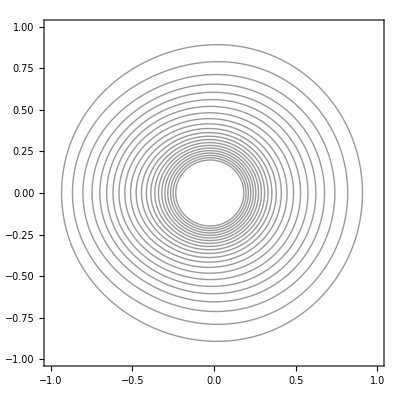

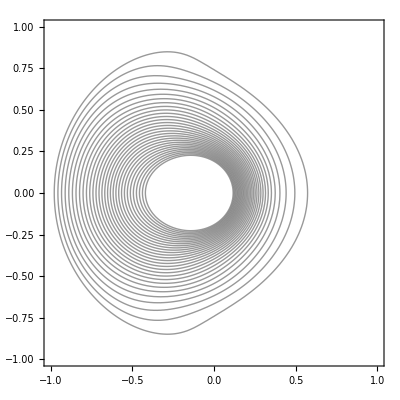

```mathematica
g3=PolarContourPlot[vζsi[r,f],{r,0,1},{f},PlotPoints->50,Contours->30]
g4=PolarContourPlot[ψsi[r,f],{r,0,1},{f},PlotPoints->50,Contours->30]
```

### Спектр на комплексной плоскости

```mathematica
Manipulate[incrs=Sort[GetIncrementsM[mat,{κ->κ1,ω->ω1,G->4,ϵ->0,Re->Re1}]//N,Re[#1]>Re[#2]&];
(*Print[Max[Re/@incrs]];*)
Show[Graphics[{PointSize[0.04],Point[{Re[#],Im[#]}]&/@incrs}],Axes->True,PlotRange->{Automatic,Automatic}]
,{κ1,0,1},{Re1,1,1000},{{ω1,0},-2,2}]
```

### Зависимость от Re

```mathematica
maxLogRe=2;
```

```mathematica
Monitor[lincRe=Table[GetIncrementsM[mat,{κ->0.5,ω->0,G->4,ϵ->0,Re->10^logRe}],{logRe,0,maxLogRe,0.1}];,logRe]
```

```mathematica
PrintRange[Transpose[{Range[0,maxLogRe,0.1],Log[Abs[Transpose[lincRe]⟦-1⟧]]}]//Re]
```

```mathematica
ListPlot[Flatten[Transpose[{Range[0,maxLogRe,0.1],#}&/@Transpose[Log[Abs[Re[lincRe]]]],{1,3,2}],1],PlotRange->All]
```

#### Инкременты Log[10, -incr] от Log[10, Re]

κ = 0.5

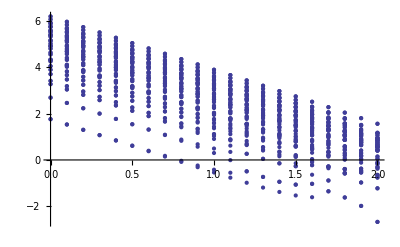
```mathematica
Show[-Graphics-,AxesLabel->{"lg Re","-lg(-λ)"},TextStyle->{FontSize->14}]
```

κ = 0.1

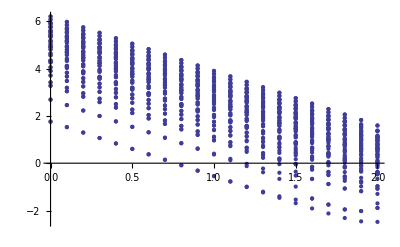

κ = 0.01

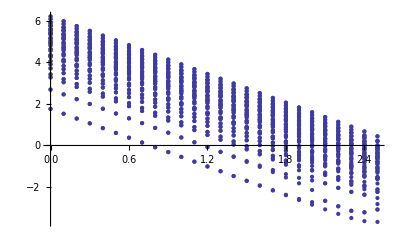

κ = 0.001

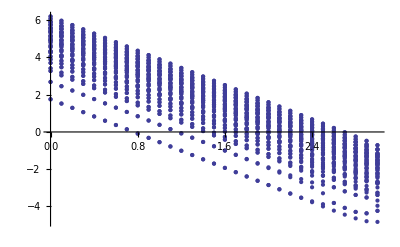

κ = 0.0

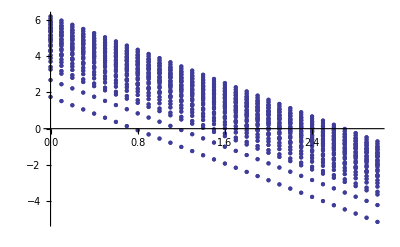

#### Подбор параметров экспоненциального затухания

```mathematica
linc=Table[{R,GetMainIncrement[100,0,1,R,2]},{R,1,20001,100}];
```

```mathematica
Timing[linc=Table[{n,(GetMainIncrement[n,0,1,1000,2])},{n,10,250,10}];]
```

```mathematica
gr=PrintRange[Last/@linc];
```

```mathematica
If[!NumericQ[E],Remove[E]];
cutout=6;
ltest=Last/@Drop[linc,cutout];
{lnaλ,λ}=CoefficientList[Fit[Log[-dif[ltest]],{1,x},x],x];
a=-E^lnaλ/λ;Print[{a,λ}];
```

```mathematica
ListPlot[ltest-Table[a E^(λ x),{x,1,Length[ltest]}]];
```

### Зависимость от тороидальности

```mathematica
lincκ=Table[GetIncrementsM[mat,{κ->kval,ω->0,G->4,ϵ->0,Re->1}],{kval,0,1,0.01}];
```

```mathematica
PrintRange[Transpose[{Range[0,1,0.01],Transpose[lincκ]⟦1⟧}]//Re]
```

```mathematica
Quadratic[l_]:=Block[{f,tmp},
f=Fit[Chop[l],{1,k,k^2},k];
tmp=Select[k/.Solve[f==0,k],(#∈Reals∧0≤#<1)&];
Return[If[Length[tmp]>0,{Coefficient[f,k^2],tmp},Coefficient[f,k^2]]]
]
```

```mathematica
ListPlot[Flatten[Transpose[{Range[0,0.1,0.01],#}&/@Transpose[Re[lincκ]],{1,3,2}],1],PlotRange->All]
```

```mathematica
Timing[GetIncrementsM[mat,{κ->0,ω->0,G->4,ϵ->0,Re->1000}];]
```

{0.046,Null}

```mathematica
ProgressIndicator[Dynamic[k1],{0,1}]
```

#### ω = 0, G=4

Re=1

```mathematica
κmax=1;dκ=0.01;
```

```mathematica
incsRe1=Monitor[Table[Take[Sort[Re/@GetIncrementsM[mat,{κ->k1,Re->1,G->4,ω->0,ϵ->0}]],-10],{k1,0,κmax,dκ}],k1];
```

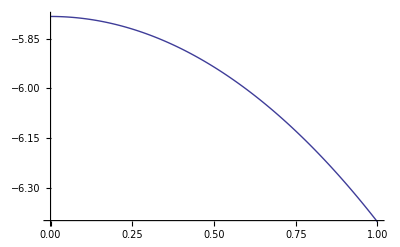

```mathematica
PrintRange[Transpose[{Range[0,κmax,dκ],Last/@incsRe1}]]
```

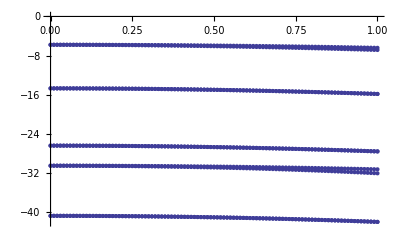

```mathematica
ListPlot[Flatten[Transpose[{Range[0,κmax,dκ],#}&/@Transpose[Re[incsRe1]],{1,3,2}],1],PlotRange->Automatic]
```

```mathematica
Reverse[Quadratic/@(Transpose[{Range[0,κmax,dκ],#}]&/@Transpose[incsRe1])]
```

{-0.629993,-0.974061,-1.1162,-1.1162,-1.16891,-1.16891,-0.770265,-1.64681,-1.26858,-1.26858}

Re=10

```mathematica
κmax=1;dκ=0.01;
```

```mathematica
incsRe10=Monitor[Table[Take[Sort[Re/@GetIncrementsM[mat,{κ->k1,Re->10,G->4,ω->0,ϵ->0}]],-10],{k1,0,κmax,dκ}],k1];
```

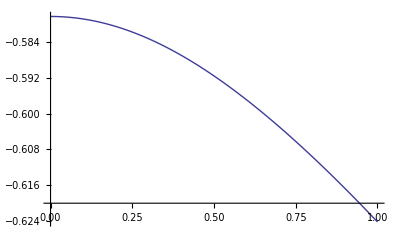

```mathematica
PrintRange[Transpose[{Range[0,κmax,dκ],Last/@incsRe10}]]
```

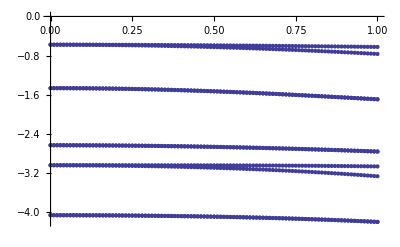

```mathematica
ListPlot[Flatten[Transpose[{Range[0,κmax,dκ],#}&/@Transpose[Re[incsRe10]],{1,3,2}],1],PlotRange->Automatic]
```

```mathematica
Reverse[Quadratic/@(Transpose[{Range[0,κmax,dκ],#}]&/@Transpose[incsRe10])]
```

{-0.0386325,-0.182137,-0.199658,-0.199658,-0.124855,-0.124855,-0.0380542,-0.242977,-0.154739,-0.154739}

Re=100

```mathematica
κmax=0.04;dκ=0.001;
```

```mathematica
incsRe100=Monitor[Table[Take[Sort[Re/@GetIncrementsM[mat,{κ->k1,Re->100,G->4,ω->0,ϵ->0}]],-10],{k1,0,κmax,dκ}],k1];
```

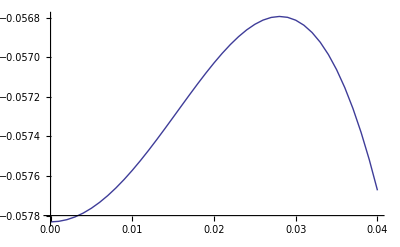

```mathematica
PrintRange[Transpose[{Range[0,κmax,dκ],#[[-1]]&/@incsRe100}]]
```

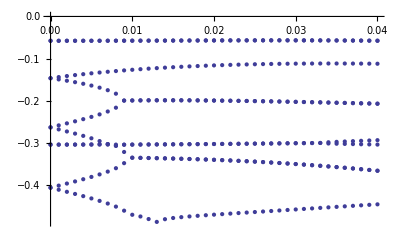

```mathematica
ListPlot[Flatten[Transpose[{Range[0,κmax,dκ],#}&/@Transpose[Re[incsRe100]],{1,3,2}],1],PlotRange->Automatic]
```

```mathematica
Reverse[Quadratic/@(Transpose[{Range[0,κmax,dκ],#}]&/@Transpose[incsRe100])]
```

{-1.7846,-1.7846,-32.7063,{68.523,{0.0836383}},-100.277,{60.383,{0.0940921}},-3.28783,{26.4644,{0.166665}},-129.154,{128.639,{0.0826153}}}

Re=1000

```mathematica
κmax=0.0004485124679;dκ=0.00001;
```

```mathematica
incsRe1000=Monitor[Table[Take[Sort[Re/@GetIncrementsM[mat,{κ->k1,Re->1000,G->4,ω->0,ϵ->0}]],-10],{k1,0,κmax,dκ}],k1];
```

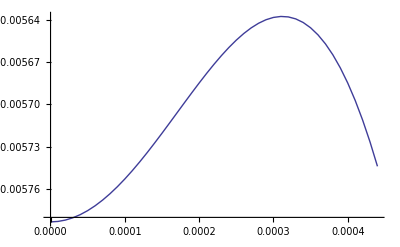

```mathematica
PrintRange[Transpose[{Range[0,κmax,dκ],Last/@incsRe1000}]]
```

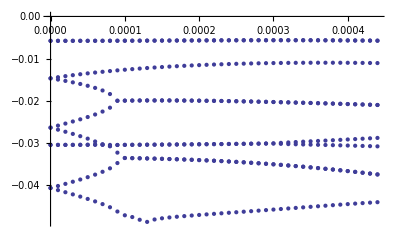

```mathematica
ListPlot[Flatten[Transpose[{Range[0,κmax,dκ],#}&/@Transpose[Re[incsRe1000]],{1,3,2}],1],PlotRange->Automatic]
```

```mathematica
Reverse[Quadratic/@(Transpose[{Range[0,κmax,dκ],#}]&/@Transpose[incsRe1000])]
```

{-1882.17,-1882.17,-29845.8,{52953.3,{0.000948323}},-83031.7,{54249.2,{0.000982591}},-8049.47,{16890.6,{0.00217466}},-110451.,{105029.,{0.000899138}}}

Re=10000

```mathematica
κmax=4.48*^-6;dκ=1.*^-7;
```

```mathematica
incsRe10000=Monitor[Table[Take[Sort[Re/@GetIncrementsM[mat,{κ->k1,Re->10000,G->4,ω->0,ϵ->0}]],-10],{k1,0,κmax,dκ}],k1];
```

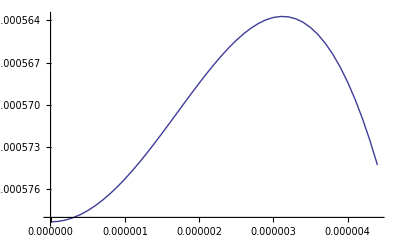

```mathematica
PrintRange[Transpose[{Range[0,κmax,dκ],Last/@incsRe10000}]]
```

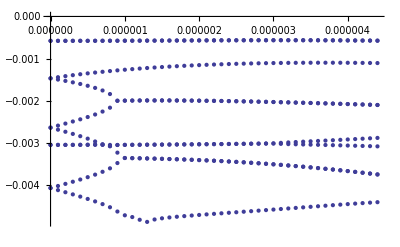

```mathematica
ListPlot[Flatten[Transpose[{Range[0,κmax,dκ],#}&/@Transpose[Re[incsRe10000]],{1,3,2}],1],PlotRange->Automatic]
```

```mathematica
Reverse[Quadratic/@(Transpose[{Range[0,κmax,dκ],#}]&/@Transpose[incsRe10000])]
```

{-1.87613×10^6,-1.87613×10^6,-2.98377×10^7,{5.29419×10^7,{9.48421×10^-6}},-8.30405×10^7,{5.42773×10^7,{9.82329×10^-6}},-8.06907×10^6,{1.68862×10^7,{0.0000217498}},-1.10453×10^8,{1.05038×10^8,{8.99082×10^-6}}}

#### ω = -1, G=4

Re=1

```mathematica
κmax=1;dκ=0.01;
```

```mathematica
incsRe1=Monitor[Table[Take[Sort[Re/@GetIncrementsM[mat,{κ->k1,Re->1,G->4,ω->-1,ϵ->0}]],-10],{k1,0,κmax,dκ}],k1];
```

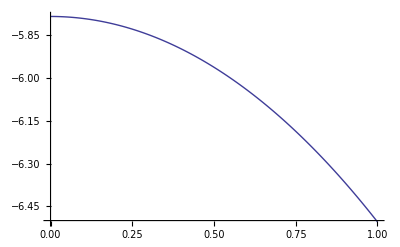

```mathematica
PrintRange[Transpose[{Range[0,κmax,dκ],Last/@incsRe1}]]
```

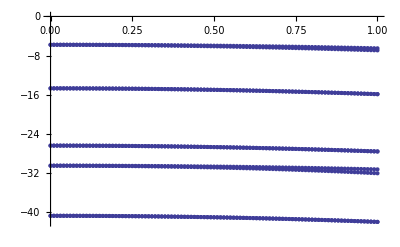

```mathematica
ListPlot[Flatten[Transpose[{Range[0,κmax,dκ],#}&/@Transpose[Re[incsRe1]],{1,3,2}],1],PlotRange->Automatic]
```

```mathematica
Reverse[Quadratic/@(Transpose[{Range[0,κmax,dκ],#}]&/@Transpose[incsRe1])]
```

{-0.728793,-1.03282,-1.16552,-1.16552,-1.18525,-1.18525,-0.790171,-1.64594,-1.27694,-1.27694}

Re=10

```mathematica
κmax=1;dκ=0.01;
```

```mathematica
incsRe10=Monitor[Table[Take[Sort[Re/@GetIncrementsM[mat,{κ->k1,Re->10,G->4,ω->-1,ϵ->0}]],-10],{k1,0,κmax,dκ}],k1];
```

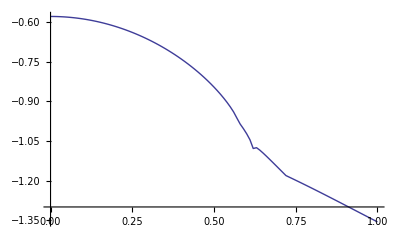

```mathematica
PrintRange[Transpose[{Range[0,κmax,dκ],Last/@incsRe10}]]
```

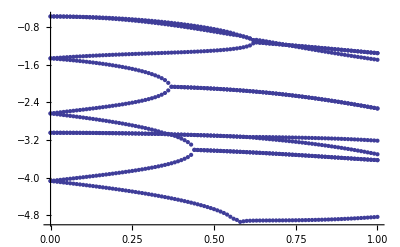

```mathematica
ListPlot[Flatten[Transpose[{Range[0,κmax,dκ],#}&/@Transpose[Re[incsRe10]],{1,3,2}],1],PlotRange->Automatic]
```

```mathematica
Reverse[Quadratic/@(Transpose[{Range[0,κmax,dκ],#}]&/@Transpose[incsRe10])]
```

{-0.394449,-0.200532,-0.891665,0.557475,-2.01591,0.855722,-0.671594,0.09648,-1.55166,1.02607}

Re=100

```mathematica
κmax=0.09;dκ=0.001;
```

```mathematica
incsRe100=Monitor[Table[Take[Sort[Re/@GetIncrementsM[mat,{κ->k1,Re->100,G->4,ω->-1,ϵ->0}]],-10],{k1,0,κmax,dκ}],k1];
```

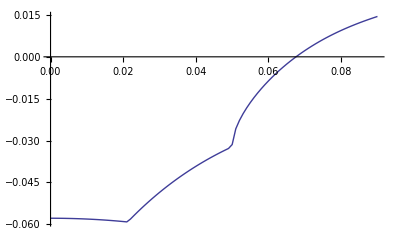

```mathematica
PrintRange[Transpose[{Range[0,κmax,dκ],#[[-1]]&/@incsRe100}]]
```

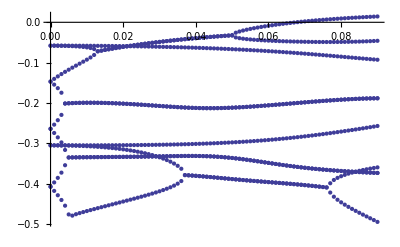

```mathematica
ListPlot[Flatten[Transpose[{Range[0,κmax,dκ],#}&/@Transpose[Re[incsRe100]],{1,3,2}],1],PlotRange->Automatic]
```

```mathematica
Reverse[Quadratic/@(Transpose[{Range[0,κmax,dκ],#}]&/@Transpose[incsRe100])]
```

{{5.83427,{0.0726063}},-8.07395,-25.3822,{15.4879,{0.161976}},{3.06439,{0.268632}},{12.9884,{0.182108}},0.343342,-6.17445,{5.61808,{0.370928}},-43.4531}

Re=1000

```mathematica
κmax=0.001;dκ=0.00001;
```

```mathematica
incsRe1000=Monitor[Table[Take[Sort[Re/@GetIncrementsM[mat,{κ->k1,Re->1000,G->4,ω->-1,ϵ->0}]],-10],{k1,0,κmax,dκ}],k1];
```

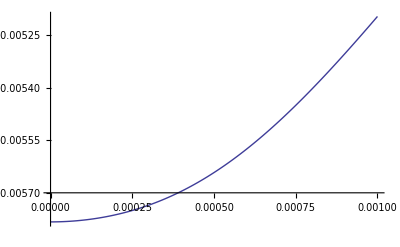

```mathematica
PrintRange[Transpose[{Range[0,κmax,dκ],#[[-1]]&/@incsRe1000}]]
```

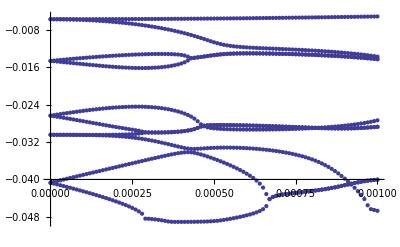

```mathematica
ListPlot[Flatten[Transpose[{Range[0,κmax,dκ],#}&/@Transpose[Re[incsRe1000]],{1,3,2}],1],PlotRange->Automatic]
```

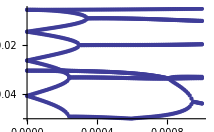
```mathematica
Export["incrs.eps",-Graphics-,ImageResolution->100,ImageSize->500]
```

incrs.eps

```mathematica
Reverse[Quadratic/@(Transpose[{Range[0,κmax,dκ],#}]&/@Transpose[incsRe1000])]
```

{{618.925,{0.00307616}},{3423.89,{0.00405562}},-4457.5,-2564.06,{2307.41,{0.00510091}},{5205.07,{0.00297196}},-1695.02,-11548.8,-16810.5,{28094.5,{0.00178435}}}

Re=10000

```mathematica
κmax=1*^-5;dκ=1.*^-7;
```

```mathematica
incsRe10000=Monitor[Table[Take[Sort[Re/@GetIncrementsM[mat,{κ->k1,Re->10000,G->4,ω->-1,ϵ->0}]],-10],{k1,0,κmax,dκ}],k1];
```

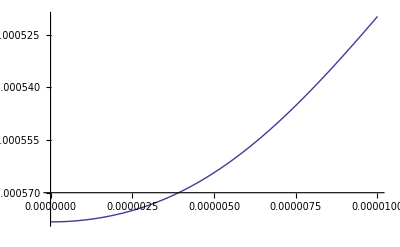

```mathematica
PrintRange[Transpose[{Range[0,κmax,dκ],Last/@incsRe10000}]]
```

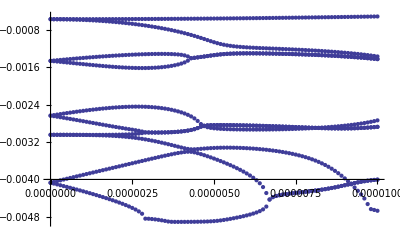

```mathematica
ListPlot[Flatten[Transpose[{Range[0,κmax,dκ],#}&/@Transpose[Re[incsRe10000]],{1,3,2}],1],PlotRange->Automatic]
```